## Dynamics of the autonomous system L = L_EH + ξ L_YM +α/m_p^2 L4_1 + κ/m_p^2 L4_2 + θ_4/m_p^2 L4^_Curv+ λ/m_p^2 L4_3 + χ_1 L_(A^4)^(1) + χ_2 L_(A^4)^(2) + χ_3/m_p^2 L_(G^2 A^2)^(1) + χ_4/m_p^2L_(G^2 A^2)^(2) + θ_1 L1^_Curv [ ϵ≡ -H^•/H^2 , P≡ ψ^(••)/(m_p H^2) , X≡ψ^•/(√2 m_p H) , Y≡ψ/(√2 m_p) , Z≡(ψ F)/(√(2 m_p H))≡(ψ (g^2 ξ-6 χ_1-2 χ_2)^(1/4))/(√(2 m_p H)) ] . S1=S2=S3=+1 . χ_(2,3,4)=θ_1=0. ξ =1. L_(A^4)^(1)=(A_μ^a A_a^μ)(A_ν^b A_b^ν) , L_(A^4)^(2)=(A_μ^a A_b^μ)(A_ν^b A_a^ν) , L_(G^2 A^2)^(1)=(A_μ^a A_νa^)(G_b^μρ G_ρ^(ν b)) , L_(G^2 A^2)^(2)=(A_μ^a A_νb^)(G_^μρb G_ρa^ν) , L4^_Curv=L_μνρσ (A^μa A^νb)(A_ρa^A_σb^) .

## 1. Initialization and global variables

```mathematica
ClearAll["Global`*"]
Needs["Notation`"]
$Assumptions=_∈Reals;
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]

(* Be careful when pasting variables from other codes that are formatted with a different style, e.g: 'gpar' printed as 'q' or 'Huble' as 'H'. *)
(* In order to convert the variables from MapleEOM to the ones from EOM, one must perform the ation {x=X; y=Y/X; z=Z/(F^4 X)}. *)

Fval=(q^2*ξ - 6 Subscript[χ, 1]-2 Subscript[χ, 2])^(1/4);
ToFs[f_]:=f/.q->Sqrt[(F^4+6 Subscript[χ, 1]+2 Subscript[χ, 2])/ξ];
NoMoreZs[f_]:=Simplify[f/.Z->Zval//ToFs,ψ∈Reals];
NoMoreFPϵ[f_]:=((f/.{P->Pval,ϵ->ϵval})//ToFs)/.{F->Fval}//Simplify; 
CCoeffs[f_]:=Collect[f,{ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]}];
ToLimit[f_]:=f/.{Z->γ X, Y->β X,ϵ->0};
```

```mathematica
fried=-1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) Subscript[θ, 1]+(-64 X Y^3-32 Y^4) Subscript[θ, 4]+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+(2*q^2*Z^4)/F^4) ξ-(4*Z^4/F^4)(3 Subscript[χ, 1]+Subscript[χ, 2])+(-4 X^2 Y^2-8 X Y^3-4 Y^4) (Subscript[χ, 3]+Subscript[χ, 4])+Subscript[Ω, m]+Subscript[Ω, r] //Expand//CCoeffs;

eq1=3-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) Subscript[θ, 1]+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) Subscript[θ, 4]+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(X^2+2 X Y+Y^2+(2*q^2*Z^4)/F^4) ξ-(4*Z^4/F^4)(3 Subscript[χ, 1]+Subscript[χ, 2])+(4 X^2 Y^2+8 X Y^3+4 Y^4)( Subscript[χ, 3]+Subscript[χ, 4])+Subscript[Ω, r]//Expand//CCoeffs;

eq2=α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) Subscript[θ, 1]+(-32 Y^3+32 Y^3 ϵ) Subscript[θ, 4]+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/√2+3 X+2 Y+(4*q^2*Z^4)/(F^4*Y)-Y ϵ) ξ-(8*Z^4/(F^4*Y))(3 Subscript[χ, 1]+Subscript[χ, 2])+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) (Subscript[χ, 3]+Subscript[χ, 4])//Expand//CCoeffs;

Print[]; Print["\nFried → ",fried," == 0"];Print["\nEq1 → ",eq1," == 0"];Print["\nEq2 → ",eq2," == 0\n"];
```

Fried → -1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) θ_1+(-64 X Y^3-32 Y^4) θ_4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ-(12 Z^4 χ_1)/F^4-(4 Z^4 χ_2)/F^4+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4+Ω_m+Ω_r == 0

Eq1 → 3-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) θ_1+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ-(12 Z^4 χ_1)/F^4-(4 Z^4 χ_2)/F^4+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4+Ω_r == 0

Eq2 → α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) θ_1+(-32 Y^3+32 Y^3 ϵ) θ_4+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ) ξ-(24 Z^4 χ_1)/(F^4 Y)-(8 Z^4 χ_2)/(F^4 Y)+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_3+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_4 == 0

```mathematica
(* Friedmann equation can be solved for Z *)
Clear[Z];solu={};Solve[fried==0,Z]//Simplify; 
For[i=1,i≤Length[%],i++,AppendTo[solu,(%[[i,1,2]]^4//Factor)]]
solu=DeleteDuplicates[solu];Zval=(solu[[1]])^(1/4)(ψ/Abs[ψ])//ToFs //Simplify; Print["\nZ == ",Zval,"\n"];

(* The real solution for Z whose magnitude is given by |Z|=(Z^4)^(1/4) and Sgn[Z]=Sgn(ψ) is selected, this is in accordance with its definition *)
```

Z == 1/(2^(1/4) Abs[ψ])ψ (1-Y^2 (6 θ_1+ξ)+4 Y^4 (8 α+8 θ_4+3 κ+χ_3+χ_4)+2 X Y (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))-X^2 (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4)))-Ω_m-Ω_r)^(1/4)

```mathematica
PyE=Solve[eq1==0&&eq2==0,{P,ϵ}]//Simplify;
Pval=PyE[[1,1,2]]//NoMoreZs;ϵval=PyE[[1,2,2]]//NoMoreZs;  
Print["\nP == ",Pval,"\n\nϵ == ",ϵval,"\n"];
```

P == -((-Y^2 (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4)) (4-12 Y^2 θ_1+Y^4 (-308 α+64 θ_4+36 κ+8 χ_3+8 χ_4)+4 X^2 (-2 θ_1+Y^2 (151 α+48 θ_4+17 κ+2 χ_3+2 χ_4))+8 X (-4 Y θ_1+Y^3 (63 α+2 (20 θ_4+8 κ+χ_3+χ_4)))-Ω_m)-2 (-1+2 Y^2 θ_1+Y^4 (62 α-2 κ)) (-X Y (-16 θ_1-ξ+2 Y^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4))+2 X^2 (ξ+Y^2 (5 α+κ-2 (χ_3+χ_4)))+2 (-1+3 Y^2 θ_1+Y^4 (77 α-16 θ_4-9 κ-2 χ_3-2 χ_4)+Ω_m+Ω_r)))/(√2 Y (-4 Y^2 (-θ_1+Y^2 (26 α+8 θ_4+3 κ)) (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))+(-1+2 Y^2 θ_1+Y^4 (62 α-2 κ)) (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4))))))

ϵ == ((-8 X Y^3 (36 α-8 θ_4-5 κ) ξ+2 X Y ξ^2-8 X Y^5 (77 α-16 θ_4-9 κ-2 χ_3-2 χ_4) (5 α+κ-2 (χ_3+χ_4))+2 Y^4 (-1526 α θ_1-320 θ_1 θ_4-102 θ_1 κ-373 α ξ-48 θ_4 ξ-11 κ ξ-4 θ_1 χ_3-4 θ_1 χ_4+2 X^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4) (5 α+κ-2 (χ_3+χ_4)))+8 Y^6 (5243 α^2+256 θ_4^2+24 κ^2+κ χ_3-2 χ_3^2+κ χ_4-4 χ_3 χ_4-2 χ_4^2+8 θ_4 (19 κ+2 (χ_3+χ_4))+α (2616 θ_4+755 κ+279 (χ_3+χ_4)))+ξ (3+X^2 (-8 θ_1+ξ)+Ω_r)-(16 θ_1+ξ-2 Y^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4)) (-1+Y^2 (6 θ_1+ξ)-4 Y^4 (8 α+8 θ_4+3 κ+χ_3+χ_4)-2 X Y (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))+X^2 (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4)))+Ω_m+Ω_r)+Y^2 (48 θ_1^2+6 κ+10 θ_1 ξ+192 X^2 θ_4 ξ+72 X^2 κ ξ+ξ^2-12 χ_3-12 χ_4+2 κ Ω_r-4 χ_3 Ω_r-4 χ_4 Ω_r+2 α (312 X^2 ξ+5 (3+Ω_r))))/(2 (ξ+2 Y^2 (5 α+8 θ_1^2+κ+θ_1 ξ-2 χ_3-2 χ_4)-2 Y^4 (406 α θ_1+128 θ_1 θ_4+46 θ_1 κ+83 α ξ+16 θ_4 ξ+5 κ ξ+4 θ_1 χ_3+4 θ_1 χ_4)+4 Y^6 (2289 α^2+256 θ_4^2+16 θ_4 (11 κ+2 (χ_3+χ_4))+κ (31 κ+10 (χ_3+χ_4))+2 α (792 θ_4+258 κ+83 (χ_3+χ_4))))))

```mathematica
Xp=P/Sqrt[2]+X ϵ ; Yp = X; Zp=Z(X/Y+ϵ/2); Ωrp=2 Subscript[Ω, r](ϵ-2); Ωmp=Subscript[Ω, m](2ϵ-3);
Print["\nX' == ",Xp,"\n\nY' == ",Yp,"\n\nZ' == ",Zp,"\n\nΩ_r' == ",Ωrp,"\n\nΩ_m' == ",Ωmp,"\n"];
```

X' == P/(√2)+X ϵ

Y' == X

Z' == Z (X/Y+ϵ/2)

Ω_r' == 2 (-2+ϵ) Ω_r

Ω_m' == (-3+2 ϵ) Ω_m

```mathematica
(* This part of the code requires 'fried' and 'eq1' to NOT depend explicitly on X,Y. i.e: It requires to avoid the rule ϵ->ϵval and P->Pval *)

Ωym =Coefficient[fried,ξ]ξ
Ωalpha = Coefficient[fried,α]α
Ωkappa = Coefficient[fried,κ]κ
Ωtheta4= Coefficient[fried,Subscript[θ, 4]] Subscript[θ, 4]
Ωchi1= Coefficient[fried,Subscript[χ, 1]] Subscript[χ, 1]
Ωchi2= Coefficient[fried,Subscript[χ, 2]] Subscript[χ, 2]
Ωchi3=Coefficient[fried,Subscript[χ, 3]] Subscript[χ, 3]
Ωchi4= Coefficient[fried,Subscript[χ, 4]] Subscript[χ, 4]
Ωtheta1=Coefficient[fried,Subscript[θ, 1]] Subscript[θ, 1]
ΩGal=1-Subscript[Ω, m]-Subscript[Ω, r]
```

(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ

(10 X^2 Y^2-188 X Y^3-32 Y^4) α

(2 X^2 Y^2-20 X Y^3-12 Y^4) κ

(-64 X Y^3-32 Y^4) θ_4

-(12 Z^4 χ_1)/F^4

-(4 Z^4 χ_2)/F^4

(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3

(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4

(8 X Y+6 Y^2) θ_1

1-Ω_m-Ω_r

```mathematica
NormalizedPym = Coefficient[eq1,ξ](ξ/3)
Palpha = Coefficient[eq1,α](α/3)
Pkappa = Coefficient[eq1,κ](κ/3)
Ptheta4 = Coefficient[eq1,Subscript[θ, 4]](Subscript[θ, 4]/3)
Pchi1= Coefficient[eq1,Subscript[χ, 1]](Subscript[χ, 1]/3)
Pchi2= Coefficient[eq1,Subscript[χ, 2]](Subscript[χ, 2]/3)
Pchi3= Coefficient[eq1,Subscript[χ, 3]](Subscript[χ, 3]/3)
Pchi4= Coefficient[eq1,Subscript[χ, 4]](Subscript[χ, 4]/3)
Ptheta1 = Coefficient[eq1,Subscript[θ, 1]](Subscript[θ, 1]/3)
PGal=(1/3) (2 ϵ-3-Subscript[Ω, r])
```

1/3 (X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ

1/3 α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)

1/3 (70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ

1/3 (192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4

-(4 Z^4 χ_1)/F^4

-(4 Z^4 χ_2)/(3 F^4)

1/3 (4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3

1/3 (4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4

1/3 (-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) θ_1

1/3 (-3+2 ϵ-Ω_r)

```mathematica
(*x=.;y=.;z=.;
Xp/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t]
ϵ/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t]
ΩGal/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t] //Simplify
PGal/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t] //Simplify*)
```

## 1.1 Critical points of the system ( PENDIENTE PENDIENTE PENDIENTE PENDIENTE PENDIENTE )

```mathematica
(* Equations for {Y',Subscript[Ω, m]',Subscript[Ω, r]'} imply that, if they exist, critical points with ϵ<<1 must have {X,Subscript[Ω, m],Subscript[Ω, r]}=0. It can be easily checked right now *)

Clear[X,Subscript[Ω, m],Subscript[Ω, r]]; Print["\n",Reduce[Yp==0&&Ωmp==0&&Ωrp==0&&ϵ<1,{X,Subscript[Ω, m],Subscript[Ω, r],ϵ}]]
X=0; Subscript[Ω, m]=0; Subscript[Ω, r]=0;κ=Subscript[Q, κ] α; Subscript[θ, 4]=Subscript[Q, 4] α; λ=Subscript[Q, λ] α;Subscript[χ, 1]=Subscript[R, 1] α; Subscript[χ, 2]=Subscript[R, 2] α; Subscript[χ, 3]=Subscript[R, 3] α; Subscript[χ, 4]=Subscript[R, 4] α; Subscript[θ, 1]=Subscript[Q, 1] α; 
Print["\nX'= ",Xp,"\n\nY'= ",Yp,"\n\nZ'= ",Zp,"\n\nΩ_r'= ",Ωrp,"\n\nΩ_m'= ",Ωmp,"\n"];
```

X==0&&Ω_m==0&&Ω_r==0&&ϵ<1

X'= P/(√2)

Y'= 0

Z'= (Z ϵ)/2

Ω_r'= 0

Ω_m'= 0

```mathematica
X=0; Subscript[Ω, m]=0; Subscript[Ω, r]=0; Print[]; ANS1=Reduce[Pval==0,Y]//Factor  (* We're interested in solutions with ϵ=0, this also sets Z'=0 *)

(* One can check that all of this solutions give rise to ϵ==2, hence, in this set of variables, there's no critical point able to drive the system of variables {X,Y,Subscript[Ω, m],Subscript[Ω, r]} towards ϵ<<1.  *)

Print["\nϵ == ",(ϵval/.{α->0,Y->YSign1/(√ξ)})/.YSign1^2->1];
Print["ϵ == ",(ϵval/.{Y->YSign1/(2 √2)√((6 Subscript[Q, 1] α+ξ+YSign2 √(-128 α-128 Subscript[Q, 4] α-48 Subscript[Q, κ] α-16 Subscript[R, 3] α-16 Subscript[R, 4] α+36 Subscript[Q, 1]^2 α^2+12 Subscript[Q, 1] α ξ+ξ^2))/((8+8 Subscript[Q, 4]+3 Subscript[Q, κ]+Subscript[R, 3]+Subscript[R, 4]) α))}/.{YSign1^2->1,YSign1^4->1,YSign1^6->1,YSign2^2->1})//Simplify];
Print["ϵ == ",ϵval/.{Y->YSign1/(√2)√((3 Subscript[Q, 1] √α+YSign2 √(308-64 Subscript[Q, 4]-36 Subscript[Q, κ]-8 Subscript[R, 3]-8 Subscript[R, 4]+9 Subscript[Q, 1]^2 α))/((-77+16 Subscript[Q, 4]+9 Subscript[Q, κ]+2 Subscript[R, 3]+2 Subscript[R, 4]) √α))}];
Print["ϵ == ",ϵval/.{Subscript[Q, 4]->1/16 (77-9 Subscript[Q, κ]-2 Subscript[R, 3]-2 Subscript[R, 4]),Y->YSign1(1/(√3 √Subscript[Q, 1] √α))}];
Print["ϵ == ",ϵval/.{Subscript[Q, 4]->1/8 (-8-3 Subscript[Q, κ]-Subscript[R, 3]-Subscript[R, 4]),Y->YSign1(1/(√(6 Subscript[Q, 1] α+ξ)))}]; Print[];
```

ϵ == 2

ϵ == ((192 ξ+(8 (48 Q_1^2 α^2+ξ^2+2 α (15+3 Q_κ-6 R_3-6 R_4+5 Q_1 ξ)) (6 Q_1 α+ξ+YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ))))/((8+8 Q_4+3 Q_κ+R_3+R_4) α)-(2 (2 Q_1 (763+160 Q_4+51 Q_κ+2 R_3+2 R_4) α+(373+48 Q_4+11 Q_κ) ξ) (6 Q_1 α+ξ+YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ)))^2)/((8+8 Q_4+3 Q_κ+R_3+R_4)^2 α)+1/((8+8 Q_4+3 Q_κ+R_3+R_4)^3 α)(5243+256 Q_4^2+24 Q_κ^2+279 R_3-2 R_3^2+279 R_4-4 R_3 R_4-2 R_4^2+Q_κ (755+R_3+R_4)+8 Q_4 (327+19 Q_κ+2 R_3+2 R_4)) (6 Q_1 α+ξ+YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ)))^3-1/((8+8 Q_4+3 Q_κ+R_3+R_4)^2 α)(-1+YSign2^2) (36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ)) (-2 Q_1 (-353+64 Q_4+27 Q_κ+26 R_3+26 R_4) α+(171+32 Q_4+11 Q_κ-2 R_3-2 R_4) ξ+(203+64 Q_4+23 Q_κ+2 R_3+2 R_4) YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ))))/(128 (ξ+((5+Q_κ-2 R_3-2 R_4+8 Q_1^2 α+Q_1 ξ) (6 Q_1 α+ξ+YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ))))/(4 (8+8 Q_4+3 Q_κ+R_3+R_4))-((2 Q_1 (203+64 Q_4+23 Q_κ+2 R_3+2 R_4) α+(83+16 Q_4+5 Q_κ) ξ) (6 Q_1 α+ξ+YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ)))^2)/(32 (8+8 Q_4+3 Q_κ+R_3+R_4)^2 α)+((2289+256 Q_4^2+31 Q_κ^2+166 R_3+166 R_4+16 Q_4 (99+11 Q_κ+2 R_3+2 R_4)+2 Q_κ (258+5 R_3+5 R_4)) (6 Q_1 α+ξ+YSign2 √(36 Q_1^2 α^2+ξ^2-4 α (32+32 Q_4+12 Q_κ+4 R_3+4 R_4-3 Q_1 ξ)))^3)/(128 (8+8 Q_4+3 Q_κ+R_3+R_4)^3 α))))

ϵ == ((1/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4)^3 α^(3/2))YSign1^6 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))^3 (5243 α^2+256 Q_4^2 α^2+24 Q_κ^2 α^2+Q_κ R_3 α^2-2 R_3^2 α^2+Q_κ R_4 α^2-4 R_3 R_4 α^2-2 R_4^2 α^2+8 Q_4 α (19 Q_κ α+2 (R_3 α+R_4 α))+α (2616 Q_4 α+755 Q_κ α+279 (R_3 α+R_4 α)))+3 ξ+(YSign1^4 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))^2 (-1526 Q_1 α^2-320 Q_1 Q_4 α^2-102 Q_1 Q_κ α^2-4 Q_1 R_3 α^2-4 Q_1 R_4 α^2-373 α ξ-48 Q_4 α ξ-11 Q_κ α ξ))/(2 (-77+16 Q_4+9 Q_κ+2 R_3+2 R_4)^2 α)+(YSign1^2 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α)) (30 α+6 Q_κ α-12 R_3 α-12 R_4 α+48 Q_1^2 α^2+10 Q_1 α ξ+ξ^2))/(2 (-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)-(16 Q_1 α-(YSign1^2 (203 α+64 Q_4 α+23 Q_κ α+2 R_3 α+2 R_4 α) (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α)))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)+ξ) (-1-(YSign1^4 (8 α+8 Q_4 α+3 Q_κ α+R_3 α+R_4 α) (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))^2)/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4)^2 α)+(YSign1^2 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α)) (6 Q_1 α+ξ))/(2 (-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(2 (1/(2 (-77+16 Q_4+9 Q_κ+2 R_3+2 R_4)^3 α^(3/2))YSign1^6 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))^3 (2289 α^2+256 Q_4^2 α^2+16 Q_4 α (11 Q_κ α+2 (R_3 α+R_4 α))+Q_κ α (31 Q_κ α+10 (R_3 α+R_4 α))+2 α (792 Q_4 α+258 Q_κ α+83 (R_3 α+R_4 α)))+ξ+(YSign1^2 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α)) (5 α+Q_κ α-2 R_3 α-2 R_4 α+8 Q_1^2 α^2+Q_1 α ξ))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)-(YSign1^4 (3 Q_1 √α+YSign2 √(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))^2 (406 Q_1 α^2+128 Q_1 Q_4 α^2+46 Q_1 Q_κ α^2+4 Q_1 R_3 α^2+4 Q_1 R_4 α^2+83 α ξ+16 Q_4 α ξ+5 Q_κ α ξ))/(2 (-77+16 Q_4+9 Q_κ+2 R_3+2 R_4)^2 α))))

ϵ == ((1/(27 Q_1^3 α^3)8 YSign1^6 (5243 α^2+24 Q_κ^2 α^2+Q_κ R_3 α^2-2 R_3^2 α^2+(77-9 Q_κ-2 R_3-2 R_4)^2 α^2+Q_κ R_4 α^2-4 R_3 R_4 α^2-2 R_4^2 α^2+1/2 (77-9 Q_κ-2 R_3-2 R_4) α (19 Q_κ α+2 (R_3 α+R_4 α))+α (755 Q_κ α+327/2 (77-9 Q_κ-2 R_3-2 R_4) α+279 (R_3 α+R_4 α)))+3 ξ+(2 YSign1^4 (-1526 Q_1 α^2-102 Q_1 Q_κ α^2-4 Q_1 R_3 α^2-20 Q_1 (77-9 Q_κ-2 R_3-2 R_4) α^2-4 Q_1 R_4 α^2-373 α ξ-11 Q_κ α ξ-3 (77-9 Q_κ-2 R_3-2 R_4) α ξ))/(9 Q_1^2 α^2)+(YSign1^2 (30 α+6 Q_κ α-12 R_3 α-12 R_4 α+48 Q_1^2 α^2+10 Q_1 α ξ+ξ^2))/(3 Q_1 α)-(16 Q_1 α-(2 YSign1^2 (203 α+23 Q_κ α+2 R_3 α+4 (77-9 Q_κ-2 R_3-2 R_4) α+2 R_4 α))/(3 Q_1 α)+ξ) (-1-(4 YSign1^4 (8 α+3 Q_κ α+R_3 α+1/2 (77-9 Q_κ-2 R_3-2 R_4) α+R_4 α))/(9 Q_1^2 α^2)+(YSign1^2 (6 Q_1 α+ξ))/(3 Q_1 α)))/(2 (1/(27 Q_1^3 α^3)4 YSign1^6 (2289 α^2+(77-9 Q_κ-2 R_3-2 R_4)^2 α^2+(77-9 Q_κ-2 R_3-2 R_4) α (11 Q_κ α+2 (R_3 α+R_4 α))+Q_κ α (31 Q_κ α+10 (R_3 α+R_4 α))+2 α (258 Q_κ α+99/2 (77-9 Q_κ-2 R_3-2 R_4) α+83 (R_3 α+R_4 α)))+ξ+(2 YSign1^2 (5 α+Q_κ α-2 R_3 α-2 R_4 α+8 Q_1^2 α^2+Q_1 α ξ))/(3 Q_1 α)-(2 YSign1^4 (406 Q_1 α^2+46 Q_1 Q_κ α^2+4 Q_1 R_3 α^2+8 Q_1 (77-9 Q_κ-2 R_3-2 R_4) α^2+4 Q_1 R_4 α^2+83 α ξ+5 Q_κ α ξ+(77-9 Q_κ-2 R_3-2 R_4) α ξ))/(9 Q_1^2 α^2))))

ϵ == ((3 ξ+1/(6 Q_1 α+ξ)^3 8 YSign1^6 (5243 α^2+24 Q_κ^2 α^2+Q_κ R_3 α^2-2 R_3^2 α^2+4 (-8-3 Q_κ-R_3-R_4)^2 α^2+Q_κ R_4 α^2-4 R_3 R_4 α^2-2 R_4^2 α^2+(-8-3 Q_κ-R_3-R_4) α (19 Q_κ α+2 (R_3 α+R_4 α))+α (755 Q_κ α+327 (-8-3 Q_κ-R_3-R_4) α+279 (R_3 α+R_4 α)))+(2 YSign1^4 (-1526 Q_1 α^2-102 Q_1 Q_κ α^2-4 Q_1 R_3 α^2-40 Q_1 (-8-3 Q_κ-R_3-R_4) α^2-4 Q_1 R_4 α^2-373 α ξ-11 Q_κ α ξ-6 (-8-3 Q_κ-R_3-R_4) α ξ))/(6 Q_1 α+ξ)^2+(YSign1^2 (30 α+6 Q_κ α-12 R_3 α-12 R_4 α+48 Q_1^2 α^2+10 Q_1 α ξ+ξ^2))/(6 Q_1 α+ξ)-(-1+YSign1^2-(4 YSign1^4 (8 α+3 Q_κ α+R_3 α+(-8-3 Q_κ-R_3-R_4) α+R_4 α))/(6 Q_1 α+ξ)^2) (16 Q_1 α+ξ-(2 YSign1^2 (203 α+23 Q_κ α+2 R_3 α+8 (-8-3 Q_κ-R_3-R_4) α+2 R_4 α))/(6 Q_1 α+ξ)))/(2 (ξ+1/(6 Q_1 α+ξ)^3 4 YSign1^6 (2289 α^2+4 (-8-3 Q_κ-R_3-R_4)^2 α^2+2 (-8-3 Q_κ-R_3-R_4) α (11 Q_κ α+2 (R_3 α+R_4 α))+Q_κ α (31 Q_κ α+10 (R_3 α+R_4 α))+2 α (258 Q_κ α+99 (-8-3 Q_κ-R_3-R_4) α+83 (R_3 α+R_4 α)))+(2 YSign1^2 (5 α+Q_κ α-2 R_3 α-2 R_4 α+8 Q_1^2 α^2+Q_1 α ξ))/(6 Q_1 α+ξ)-(2 YSign1^4 (406 Q_1 α^2+46 Q_1 Q_κ α^2+4 Q_1 R_3 α^2+16 Q_1 (-8-3 Q_κ-R_3-R_4) α^2+4 Q_1 R_4 α^2+83 α ξ+5 Q_κ α ξ+2 (-8-3 Q_κ-R_3-R_4) α ξ))/(6 Q_1 α+ξ)^2)))

```mathematica
Print[]; ANS2=Reduce[Pval==0 &&ϵval==0 ,Y]//Factor

(* One can check that all of this solutions give rise to ϵ==2, hence, in this set of variables, there's no critical point able to drive the system of variables {X,Y,Subscript[Ω, m],Subscript[Ω, r]} towards ϵ<<1.  *)

Print["ϵ == ",Simplify[ϵval/.{α->0,Y->YSign1/(√2)√((3 Subscript[Q, 1] √α+YSign2 √(308-64 Subscript[Q, 4]-36 Subscript[Q, κ]-8 Subscript[R, 3]-8 Subscript[R, 4]+9 Subscript[Q, 1]^2 α))/((-77+16 Subscript[Q, 4]+9 Subscript[Q, κ]+2 Subscript[R, 3]+2 Subscript[R, 4]) √α))},{YSign1^2==1,YSign2^2==1}]];
Print["ϵ == ",Simplify[ϵval/.{α->0,Subscript[Q, 4]->1/16 (77-9 Subscript[Q, κ]-2 Subscript[R, 3]-2 Subscript[R, 4]),Y->YSign1(1/(√3 √Subscript[Q, 1] √α))},YSign1^2==1]];
Print["ϵ == ",Simplify[ϵval/.{α->0,Subscript[Q, 4]->1/8 (-8-3 Subscript[Q, κ]-Subscript[R, 3]-Subscript[R, 4]),Y->YSign1(1/(√(6 Subscript[Q, 1] α+ξ)))},YSign1^2==1]]; Print[];
```

((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) α≠0&&(Y==-(√((3 Q_1 √α-√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2)||Y==(√((3 Q_1 √α-√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2)||Y==-(√((3 Q_1 √α+√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2)||Y==(√((3 Q_1 √α+√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2))&&-89992 Q_1 α-25728 Q_1 Q_4 α+1024 Q_1 Q_4^2 α-5968 Q_1 Q_κ α+1664 Q_1 Q_4 Q_κ α+456 Q_1 Q_κ^2 α-984 Q_1 R_3 α+256 Q_1 Q_4 R_3 α+136 Q_1 Q_κ R_3 α+16 Q_1 R_3^2 α-984 Q_1 R_4 α+256 Q_1 Q_4 R_4 α+136 Q_1 Q_κ R_4 α+32 Q_1 R_3 R_4 α+16 Q_1 R_4^2 α+764302 Y^2 α+316736 Q_4 Y^2 α-19968 Q_4^2 Y^2 α-16384 Q_4^3 Y^2 α+74522 Q_κ Y^2 α-37888 Q_4 Q_κ Y^2 α-19968 Q_4^2 Q_κ Y^2 α-10990 Q_κ^2 Y^2 α-7744 Q_4 Q_κ^2 Y^2 α-954 Q_κ^3 Y^2 α+6020 R_3 Y^2 α-2944 Q_4 R_3 Y^2 α-5120 Q_4^2 R_3 Y^2 α-1736 Q_κ R_3 Y^2 α-4224 Q_4 Q_κ R_3 Y^2 α-860 Q_κ^2 R_3 Y^2 α-56 R_3^2 Y^2 α-512 Q_4 R_3^2 Y^2 α-216 Q_κ R_3^2 Y^2 α-16 R_3^3 Y^2 α+6020 R_4 Y^2 α-2944 Q_4 R_4 Y^2 α-5120 Q_4^2 R_4 Y^2 α-1736 Q_κ R_4 Y^2 α-4224 Q_4 Q_κ R_4 Y^2 α-860 Q_κ^2 R_4 Y^2 α-112 R_3 R_4 Y^2 α-1024 Q_4 R_3 R_4 Y^2 α-432 Q_κ R_3 R_4 Y^2 α-48 R_3^2 R_4 Y^2 α-56 R_4^2 Y^2 α-512 Q_4 R_4^2 Y^2 α-216 Q_κ R_4^2 Y^2 α-48 R_3 R_4^2 Y^2 α-16 R_4^3 Y^2 α+364840 Q_1^2 Y^2 α^2+37760 Q_1^2 Q_4 Y^2 α^2+1024 Q_1^2 Q_4^2 Y^2 α^2-4272 Q_1^2 Q_κ Y^2 α^2-384 Q_1^2 Q_4 Q_κ Y^2 α^2-72 Q_1^2 Q_κ^2 Y^2 α^2-1976 Q_1^2 R_3 Y^2 α^2+256 Q_1^2 Q_4 R_3 Y^2 α^2+168 Q_1^2 Q_κ R_3 Y^2 α^2+16 Q_1^2 R_3^2 Y^2 α^2-1976 Q_1^2 R_4 Y^2 α^2+256 Q_1^2 Q_4 R_4 Y^2 α^2+168 Q_1^2 Q_κ R_4 Y^2 α^2+32 Q_1^2 R_3 R_4 Y^2 α^2+16 Q_1^2 R_4^2 Y^2 α^2-6853 ξ-2272 Q_4 ξ+768 Q_4^2 ξ-662 Q_κ ξ+736 Q_4 Q_κ ξ+171 Q_κ^2 ξ+24 R_3 ξ+128 Q_4 R_3 ξ+56 Q_κ R_3 ξ+4 R_3^2 ξ+24 R_4 ξ+128 Q_4 R_4 ξ+56 Q_κ R_4 ξ+8 R_3 R_4 ξ+4 R_4^2 ξ+50204 Q_1 Y^2 α ξ-5504 Q_1 Q_4 Y^2 α ξ-1024 Q_1 Q_4^2 Y^2 α ξ-4944 Q_1 Q_κ Y^2 α ξ-768 Q_1 Q_4 Q_κ Y^2 α ξ-108 Q_1 Q_κ^2 Y^2 α ξ-1612 Q_1 R_3 Y^2 α ξ-64 Q_1 Q_4 R_3 Y^2 α ξ+12 Q_1 Q_κ R_3 Y^2 α ξ+8 Q_1 R_3^2 Y^2 α ξ-1612 Q_1 R_4 Y^2 α ξ-64 Q_1 Q_4 R_4 Y^2 α ξ+12 Q_1 Q_κ R_4 Y^2 α ξ+16 Q_1 R_3 R_4 Y^2 α ξ+8 Q_1 R_4^2 Y^2 α ξ≠0)||(Q_4==1/16 (77-9 Q_κ-2 R_3-2 R_4)&&Q_1 α≠0&&(Y==-1/(√3 √Q_1 √α)||Y==1/(√3 √Q_1 √α))&&63364-3656 Q_κ+52 Q_κ^2-744 R_3+24 Q_κ R_3-744 R_4+24 Q_κ R_4-6042 Q_1^2 α+174 Q_1^2 Q_κ α+36 Q_1^2 R_3 α+36 Q_1^2 R_4 α+144 Q_1^4 α^2-960 Q_1 ξ+24 Q_1 Q_κ ξ+12 Q_1 R_3 ξ+12 Q_1 R_4 ξ+45 Q_1^3 α ξ≠0)

## 2. Viability of the asymptotic behaviour ( Y → βX , Z → γX )

```mathematica
Clear[P,β,γ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],q,ξ]; 
(* It's easy to show that, if a behaviour like {Y->βX,Z->γX} happens, then ϵ->0 and the autonomous system tends to the following: *)
XpLimit=P/Sqrt[2]; YpLimit=X; ZpLimit=(γ/β)X; Print["\nX' → ",XpLimit,"\n\nY' → ",YpLimit,"\n\nZ' → ",ZpLimit,"\n"] 

(* Given that "fried" and "XpLimit/X" only depend on even powers of X, the following computations hold for X->±∞ *)
κ=Subscript[Q, κ] α; Subscript[θ, 4]=Subscript[Q, 4] α; λ=Subscript[Q, λ] α;Subscript[χ, 1]=Subscript[C, 1] α; Subscript[χ, 2]=Subscript[C, 2] α; Subscript[χ, 3]=Subscript[C, 3] α; Subscript[χ, 4]=Subscript[C, 4] α; Subscript[θ, 1]=Subscript[Q, 1] α;ξ=Subscript[Q, ξ] α; Subscript[C, 4]=Subscript[C, 34]-Subscript[C, 3];
```

X' → P/(√2)

Y' → X

Z' → (X γ)/β

```mathematica
Solve[(eq1//ToFs//ToLimit)==0,{P}] //Simplify;
P=%[[1,1,2]]; Print["\nEq3 →  ",(eq3=(1/β)-Limit[XpLimit/X,X->Infinity]==0//Simplify)]
 Clear[P]; (* Y'->βX' & Y'=X  => (1/β-X'/X)-> 0 <=> β,X ≠ 0 *)

Solve[(eq2//ToFs//ToLimit)==0,{P}];
P=%[[1,1,2]]; Print["\nEq4 →  ",(eq4=(1/β)-Limit[XpLimit/X,X->Infinity]==0//Simplify)]
 Clear[P]; (* Z'->γX' && Z'->(γ/β)X => (1/β-X'/X)-> 0 <=> β,X ≠ 0 *)

Print["\nEq5 →  ",(eq5=Limit[(fried//ToFs//ToLimit)/(X^4),X->Infinity]==0//Simplify),"\n"]
```

Eq3 →  (α β^2 (411+47 Q_κ+158 β+54 Q_κ β-170 β^2+12 Q_κ β^2+2 C_34 (1+β)^2+16 Q_4 (8+8 β+β^2))+γ^4)/((26+8 Q_4+3 Q_κ) α β)==0

Eq4 →  (α β^2 (-10-15 β+109 β^2+16 Q_4 β^2+2 C_34 (2+3 β+β^2)+Q_κ (-2-3 β+3 β^2))-2 γ^4)/((-5+2 C_34-Q_κ) α β)==0

Eq5 →  α β^2 (-5+94 β+32 Q_4 β+16 β^2+16 Q_4 β^2+2 C_34 (1+β)^2+Q_κ (-1+10 β+6 β^2))==γ^4

It's easy to show that  { Y→β X , Z→γX }  implies ϵ=0  ( ω=-1 )  but also  X[N]=X_0 e^(N/β) , therefore...   X[+∞]→Piecewise[{{Sgn(X_0)∞, ⇔  β>0}, {0, ⇔  β<0}}]    and   X[-∞]→Piecewise[{{0, ⇔  β>0}, {Sgn(X_0)∞, ⇔  β<0}}]   

Taking into account that  X≠0  is required to compute {Eq3,Eq4,Eq5}, this asymptotic behaviour is theoretically able to produce Inflation (with β<0) and Dark energy (with β>0),
Inflation happens at early times  (N→-∞)  and Dark energy happens at late times   (N→∞); other scenarios would require (X→0) and hence, would be mathematically flawed

Also, notice that the discard of   X=0  solutions can be argued from a physical point of view
Allowing  X→0  implies a trivial solution  with {X,Y,Z}→0  , {ψ,ψ'}→0 , ΩGal→0   and  Ω_r+Ω_m→1,then, ϵ→1/2 (3+Ω_r)  <<1 ⇔ Ω_r<<-1  which is, by definition, impossible.

```mathematica
Print[];ϵval/.{X->0,Y->0,Z->0}//Simplify
fried==0/.{X->0,Y->0,Z->0}
Simplify[ϵval/.{X->0,Y->0,Z->0},%]
Reduce[%<1]
Print[];
```

-(Q_ξ (-4+Ω_m)+16 Q_1 (-1+Ω_m+Ω_r))/(2 Q_ξ)

-1+Ω_m+Ω_r==0

1/2 (3+Ω_r)

Ω_r<-1

Notice that  Y_limit/Z_limit=β/γ= 1/F √(H/m_p)>0  implies that   Sgn(Y_limit)=Sgn(Z_limit)   and  Sgn(β)=Sgn(γ)   but, by definition, Sgn(Y) = Sgn(Z)=Sgn(ψ) , so

Sgn(Y_limit)=Sgn(Z_limit)=Sgn(β)Sgn(X_0)=Sgn(γ)Sgn(X_0)=Sgn(ψ),  implying that   Sgn(β)=Sgn(γ)=Sgn(ψ/(ψ̇))=Sgn(ψ/X_0)  and  Sgn(ψ̇)=Sgn(X_0)=Sgn(X)

This means that, given this tendency, the sign of X_0 determines if ψ will monotonically increase or decrease over time.

```mathematica
Print[]; asymptotes=Solve[eq3&&eq4&&eq5/.{γ->γ4^(1/4)},{β,γ4}]//Simplify; Print["Number of soutions found: ",Length[asymptotes]," - The first one was assigned to γval. \n"]
Print["β = ",βval=asymptotes[[1,1,2]]//Simplify,"\n"];
Print["γ = ",γval=asymptotes[[1,2,2]]^(1/4)//Simplify,"\n"];
Print[];
```

Number of soutions found: 1 - The first one was assigned to γval.

β = (203+2 C_34+64 Q_4+23 Q_κ)/(77-2 C_34-16 Q_4-9 Q_κ)

γ = (-1/(-77+2 C_34+16 Q_4+9 Q_κ)^4(203+2 C_34+64 Q_4+23 Q_κ)^2 (-2099013-32768 Q_4^3-548709 Q_κ-45455 Q_κ^2-1023 Q_κ^3+4 C_34^2 (83+16 Q_4+5 Q_κ)-256 Q_4^2 (1709+121 Q_κ)-16 Q_4 (109095+17482 Q_κ+611 Q_κ^2)-4 C_34 (36911+896 Q_4^2+3404 Q_κ+67 Q_κ^2+16 Q_4 (741+31 Q_κ))) α)^(1/4)

```mathematica
Print[]; 
sols1=Reduce[βval<0&&γval^2>0,{α,Subscript[Q, κ],Subscript[Q, 4],Subscript[C, 34]},Backsubstitution->True];
sols2=Reduce[βval>0&&γval^2>0,{α,Subscript[Q, κ],Subscript[Q, 4],Subscript[C, 34]},Backsubstitution->True];
(* In Addition, it's required that F^2>0 to have H/Subscript[m, p]>0 *)
Length[sols1]
Length[sols2]
Print[];
```

46

8

```mathematica
Clear[P1,P2,Subscript[Q, 4],Subscript[Q, κ]] (* Subscript[Q, 4] y Rangoβ provienen de consideraciones de estabilidad *)

Subscript[Q, 4]=5/4(Subscript[Q, κ]-1);

Rangoβ=Reduce[β>0&&((Subscript[Q, κ]<81&&α>0)||(Subscript[Q, κ]>81&&α<0))]; Print[]; Print["La ventana de parámetros adecuada para tener [ β>0, C_T^2=1 y m_p^2>0 ] exige: [ ",Rangoβ," ] "]

SS=StringSplit[ToString[N[Rangoβ,60]],{"< Q⎵Subscript⎵κ <","&& "}];
Qi=Rationalize[ToExpression[SS[[Length[SS]-1]]]];
Qf=Rationalize[ToExpression[SS[[Length[SS]]]]];

P1=2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2);
P2=203+64 Subscript[Q, 4]+23 Subscript[Q, κ];

flag=0;
If[Reduce[Rangoβ&&P1>0&&P2>0]==False,{flag=1;Print[" ⇒  Es imposible tener P1>0 && P2>0"]}];
If[Reduce[Rangoβ&&P1>0&&P2<0]==False,{flag=1;Print[" ⇒  Es imposible tener P1>0 && P2<0"]}];
If[Reduce[Rangoβ&&P1<0&&P2>0]==False,{flag=1;Print[" ⇒  Es imposible tener P1<0 && P2>0"]}];
If[Reduce[Rangoβ&&P1<0&&P2<0]==False,{flag=1;Print[" ⇒  Es imposible tener P1<0 && P2<0"]}];
If[flag==0,Print["Esto implica que no hay restricciones sobre los posibles signos relativos de {P1,P2} - Info que es útil para analizar γ."]];
Print[];
```

La ventana de parámetros adecuada para tener [ β>0, C_T^2=1 y m_p^2>0 ] exige: [ β>0&&((α<0&&Q_κ>81)||(α>0&&Q_κ<81)) ]

Esto implica que no hay restricciones sobre los posibles signos relativos de {P1,P2} - Info que es útil para analizar γ.

```mathematica
Clear[P1,P2]

calc1=Reduce[Re[-((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]>0&&Im[((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]==0&&((P1>0&&P2>0)||(P1<0&&P2>0))];
calc2=Reduce[Re[((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]>0&&Im[((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]==0&&((P1>0&&P2>0)||(P1<0&&P2>0))];
calc3=Reduce[Re[-((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]>0&&Im[((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]==0&&((P1>0&&P2>0)||(P1<0&&P2>0))];
calc4=Reduce[Re[((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]>0&&Im[((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- 1)^(1/4)]==0&&((P1>0&&P2>0)||(P1<0&&P2>0))];

Print[];
 Rangoγ1=Reduce[calc1&&α∈Reals ,{α,P1,P2}]//Simplify; Print[" [ γ_1>0 ∈ ℝ ] ⇔ ",Rangoγ1];
 Rangoγ2=Reduce[calc2&&α∈Reals ,{α,P1,P2}]//Simplify; Print[" [ γ_2>0 ∈ ℝ ] ⇔ ",Rangoγ2];
 Rangoγ3=Reduce[calc3&&α∈Reals ,{α,P1,P2}]//Simplify; Print[" [ γ_3>0 ∈ ℝ ] ⇔ ",Rangoγ3];
 Rangoγ4=Reduce[calc4&&α∈Reals ,{α,P1,P2}]//Simplify; Print[" [ γ_4>0 ∈ ℝ ] ⇔ ",Rangoγ4];
Print[];
```

[ γ_1>0 ∈ ℝ ] ⇔ False

[ γ_2>0 ∈ ℝ ] ⇔ α>0&&P1>0&&P2>0

[ γ_3>0 ∈ ℝ ] ⇔ α<0&&P1<0&&P2>0

[ γ_4>0 ∈ ℝ ] ⇔ False

```mathematica
Print[]; Clear[P1,P2];

P1=2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2);
P2=203+64 Subscript[Q, 4]+23 Subscript[Q, κ];

Rangoβγ1=Reduce[ Rangoγ1&&Rangoβ,{α,Subscript[Q, κ]} ]; Print[" [ γ_1>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ1];
Rangoβγ2=Reduce[ Rangoγ2&&Rangoβ,{α,Subscript[Q, κ]} ]; Print[" [ γ_2>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ2];
Rangoβγ3=Reduce[ Rangoγ3&&Rangoβ,{α,Subscript[Q, κ]} ]; Print[" [ γ_3>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ3];
Rangoβγ4=Reduce[ Rangoγ4&&Rangoβ,{α,Subscript[Q, κ]} ]; Print[" [ γ_4>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ4];
Print[];
```

[ γ_1>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ False

[ γ_2>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ β>0&&α>0&&1/651 (-738+√83085)<Q_κ<81

[ γ_3>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ False

[ γ_4>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ False

```mathematica
Clear[g,Ho,mp]; BetaSobreGamma=Simplify[(β/solγ[2])^2//Factor,1/651 (-738+√83085)<Subscript[Q, κ]<97/29];

gp=√((Ho^2 (536713+1254169 Subscript[Q, κ]+777675 Subscript[Q, κ]^2+125643 Subscript[Q, κ]^3)+6 mp^2 Subscript[Q, 1](123+103 Subscript[Q, κ])^2)/(mp^2 (123+103 Subscript[Q, κ])^2 Subscript[Q, ξ]));
RangosgReal=Reduce[gp^2>0&&1/651 (-738+√83085)<Subscript[Q, κ]<97/29&&Ho>0&&mp>0&&α>0,{α,mp,Ho,Subscript[Q, κ],Subscript[Q, 1],Subscript[Q, ξ]}]//Factor;

Print["
β/γ_2 = ",BetaSobreGamma," = Ho/(mp SuperscriptBox[(SuperscriptBox[g, 2] ξ - 6 SubscriptBox[χ, 1]), 1/2])  >>> Implica g = ± ",gp,"


En donde [ g ∈ ℝ ] siempre y cuando... 
",RangosgReal,"

Para el caso de interés ξ=1 implica [ Q_1 ≳ -10^-120 ]
"];
```

β/γ_2 = β^2/solγ[2]^2 = Ho/(mp SuperscriptBox[(SuperscriptBox[g, 2] ξ - 6 SubscriptBox[χ, 1]), 1/2])  >>> Implica g = ± √((6 mp^2 Q_1 (123+103 Q_κ)^2+Ho^2 (536713+1254169 Q_κ+777675 Q_κ^2+125643 Q_κ^3))/(mp^2 (123+103 Q_κ)^2 Q_ξ))


En donde [ g ∈ ℝ ] siempre y cuando... 
α>0&&mp>0&&Ho>0&&1/651 (-738+√83085)<Q_κ<97/29&&((Q_1<-(Ho^2 (757+193 Q_κ) (709+1476 Q_κ+651 Q_κ^2))/(6 mp^2 (123+103 Q_κ)^2)&&Q_ξ<0)||(Q_1>-(Ho^2 (757+193 Q_κ) (709+1476 Q_κ+651 Q_κ^2))/(6 mp^2 (123+103 Q_κ)^2)&&Q_ξ>0))

Para el caso de interés ξ=1 implica [ Q_1 ≳ -10^-120 ]

```mathematica
Subscript[θ, 4]=Subscript[Q, 4] α; λ=Subscript[Q, λ] α; κ=Subscript[Q, κ] α; Subscript[χ, 1]=Subscript[Q, 1]*α; ξ=Subscript[Q, ξ]*α;
RangosGabriel=α>0&&((κ≤0&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/2 (5 α-κ))||(0<κ<(757 α)/2141-(64 √(699/5) √(α^2))/2141&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/64 (19 α-112 Subscript[θ, 4]+53 κ)+1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||(κ==(757 α)/2141-(64 √(699/5) √(α^2))/2141&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&λ==1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||(κ==(757 α)/2141+(64 √(699/5) √(α^2))/2141&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&λ==1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||((757 α)/2141+(64 √(699/5) √(α^2))/2141<κ<α&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/64 (19 α-112 Subscript[θ, 4]+53 κ)+1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||(α≤κ<81 α&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/2 (5 α-κ)));
```

```mathematica
soluciones=Reduce[α>0&&1/651 (-738+√83085)<Subscript[Q, κ]<97/29&&Subscript[Q, 4]==5/4(Subscript[Q, κ]-1)&&RangosGabriel]; Print[];
For[i=1,i≤Length[soluciones],i++,

Clear[Qvalue,Qκi,Qκf];
soli=soluciones[[i]]//Factor;soliparts=Cases[soli,_];
For[ii=1,ii≤Length[soliparts],ii++,If[Cases[soliparts[[ii]],Subscript[Q, κ]]≠ {},RangoQκ=soliparts[[ii]]];If[Cases[soliparts[[ii]],Subscript[Q, λ]]≠ {},RangoQλ=soliparts[[ii]]]];
SSκequality=StringSplit[ToString[N[RangoQκ]],{"Q⎵Subscript⎵κ"," == "}];
SSλequality=StringSplit[ToString[N[RangoQλ]],{"Q⎵Subscript⎵κ"," == "}];
If[
Length[SSκequality]==1,
Qvalue=RangoQκ[[2]];Print[StringForm[" ``    ",i],soli,StringForm["&& Q_4≃ ``",N[5/4(Qvalue-1),3]]],
Qκi=RangoQκ[[1]];Qκf=RangoQκ[[5]]; Qλi=RangoQλ[[1]];Qλf=RangoQλ[[5]];
Print[StringForm[" ``    ",i],soli,StringForm["&& `` ≲ Q_4 ≲ ``",N[5/4(Qκi-1),3],N[5/4(Qκf-1),3]]]
]]; Print[];
Print["En particular, la solución 4 es atractiva porque permite Q_4= 5/4(Q_κ-1)= 0 && ",Reduce[1≤Subscript[Q, κ]<97/29&&1/64 (159-87 Subscript[Q, κ]-√(1-7570 Subscript[Q, κ]+10705 Subscript[Q, κ]^2))≤Subscript[Q, λ]≤1/2 (5-Subscript[Q, κ])&&Subscript[Q, 4]==5/4(Subscript[Q, κ]-1)&&Subscript[Q, κ]∈Integers&&Subscript[Q, λ]∈Integers&&Subscript[Q, 4]∈Integers,{Subscript[Q, κ],Subscript[Q, λ]}],"

Las otras soluciones pueden tener proporciones enteras? // Bajo qué circunstancias?"];

For[i=1,i≤Length[soluciones],i++,

Print[i,". ",Reduce[soluciones[[i]]&&Subscript[Q, 4]==(5/4)(Subscript[Q, κ]-1)&&Subscript[Q, κ]∈Integers&&Subscript[Q, λ]∈Integers&&Subscript[Q, 4]∈Integers]]]; Print[];
```

α>0&&Q_κ==(3785-64 √3495)/10705&&Q_λ==(3 (7150+29 √3495))/10705&& Q_4≃ -1.25

α>0&&Q_κ==(3785+64 √3495)/10705&&Q_λ==-(3 (-7150+29 √3495))/10705&& Q_4≃ -0.366

1/651 (-738+√83085)<Q_κ≤0&&1/64 (159-87 Q_κ-√(1-7570 Q_κ+10705 Q_κ^2))≤Q_λ≤1/2 (5-Q_κ)&&α>0&& -2.11 ≲ Q_4 ≲ -1.25

1≤Q_κ<97/29&&1/64 (159-87 Q_κ-√(1-7570 Q_κ+10705 Q_κ^2))≤Q_λ≤1/2 (5-Q_κ)&&α>0&& 0 ≲ Q_4 ≲ 2.93

0<Q_κ<(3785-64 √3495)/10705&&1/64 (159-87 Q_κ-√(1-7570 Q_κ+10705 Q_κ^2))≤Q_λ≤1/64 (159-87 Q_κ+√(1-7570 Q_κ+10705 Q_κ^2))&&α>0&& -1.25 ≲ Q_4 ≲ -1.25

(3785+64 √3495)/10705<Q_κ<1&&1/64 (159-87 Q_κ-√(1-7570 Q_κ+10705 Q_κ^2))≤Q_λ≤1/64 (159-87 Q_κ+√(1-7570 Q_κ+10705 Q_κ^2))&&α>0&& -0.366 ≲ Q_4 ≲ 0

En particular, la solución 4 es atractiva porque permite Q_4= 5/4(Q_κ-1)= 0 && (Q_κ==1&&Q_λ==1)||(Q_κ==1&&Q_λ==2)

Las otras soluciones pueden tener proporciones enteras? // Bajo qué circunstancias?

1. False

2. False

3. False

4. (Q_λ==1&&Q_κ==1&&α>0)||(Q_λ==2&&Q_κ==1&&α>0)

5. False

6. False

## 3. Solución numérica - N.ba I ( programado para ejecutarse después de 1 y 2 )

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"Qi"|"Qf"|"asintotas"];

soln[t0_,Ωr0_,Ωm0_,x0_,y0_,ξ_,g_,α_,κ_,θ4_,χ1_,χ2_,χ3_,χ4_,θ1_]:=NDSolve[
{
 x'[t]==(y[t] (-4 Subscript[θ, 1]-ξ+2 (47 α+16 Subscript[θ, 4]+5 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) y[t]^2) (-4+12 Subscript[θ, 1] y[t]^2+4 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 3]-2 Subscript[χ, 4]) y[t]^4-4 x[t]^2 (-2 Subscript[θ, 1]+(151 α+48 Subscript[θ, 4]+17 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^2)-8 x[t] (-4 Subscript[θ, 1] y[t]+(63 α+2 (20 Subscript[θ, 4]+8 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3)+Ωm[t])-1/((g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) y[t])2 (-1+2 Subscript[θ, 1] y[t]^2+(62 α-2 κ) y[t]^4) (g^2 ξ (x[t] y[t] (16 Subscript[θ, 1]+ξ-2 (203 α+64 Subscript[θ, 4]+23 κ-8 Subscript[χ, 3]-8 Subscript[χ, 4]) y[t]^2)+2 x[t]^2 (ξ+(5 α+κ+2 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2)+2 (-1+3 Subscript[θ, 1] y[t]^2+(77 α-16 Subscript[θ, 4]-9 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^4+Ωm[t]+Ωr[t]))-2 (3 Subscript[χ, 1] (x[t] y[t] (16 Subscript[θ, 1]+ξ-2 (203 α+64 Subscript[θ, 4]+23 κ-8 Subscript[χ, 3]-8 Subscript[χ, 4]) y[t]^2)+2 x[t]^2 (ξ+(5 α+κ+2 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2)+2 (-1+3 Subscript[θ, 1] y[t]^2+(77 α-16 Subscript[θ, 4]-9 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^4+Ωm[t]+Ωr[t]))+Subscript[χ, 2] (x[t] y[t] (16 Subscript[θ, 1]-5 ξ-2 (233 α+64 Subscript[θ, 4]+29 κ-40 Subscript[χ, 3]-40 Subscript[χ, 4]) y[t]^2)+2 x[t]^2 (ξ-(5 α+κ-14 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2)+2 (-1-(3 Subscript[θ, 1]+2 ξ) y[t]^2+(295 α+16 Subscript[θ, 4]-3 κ+14 Subscript[χ, 3]+14 Subscript[χ, 4]) y[t]^4+Ωm[t]+Ωr[t]))))-1/(g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2]))x[t] (g^2 ξ (-16 Subscript[θ, 1]-4 ξ+24 Subscript[θ, 1] ξ x[t]^2+8 Subscript[θ, 1] (16 Subscript[θ, 1]+5 ξ) x[t] y[t]-8 (α (782 Subscript[θ, 1]+89 ξ)+ξ (48 Subscript[θ, 4]+19 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4]+43 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3-4 (-26 α Subscript[θ, 1]+160 Subscript[θ, 1] Subscript[θ, 4]+66 Subscript[θ, 1] κ-77 α ξ+16 Subscript[θ, 4] ξ+9 κ ξ+16 Subscript[θ, 1] Subscript[χ, 3]+2 ξ Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 4]+2 ξ Subscript[χ, 4]+2 (1015 α^2+23 κ^2-54 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-54 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+α (320 Subscript[θ, 4]+318 κ-490 (Subscript[χ, 3]+Subscript[χ, 4]))+32 Subscript[θ, 4] (2 κ-5 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t]^2) y[t]^4+16 (4963 α^2+512 Subscript[θ, 4]^2+53 κ^2+38 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+38 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2+48 Subscript[θ, 4] (7 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1544 Subscript[θ, 4]+532 κ+17 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^5-8 (3619 α^2-256 Subscript[θ, 4]^2-45 κ^2-22 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-22 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2-32 Subscript[θ, 4] (7 κ+Subscript[χ, 3]+Subscript[χ, 4])+α (480 Subscript[θ, 4]-38 κ+422 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6+16 Subscript[θ, 1] Ωm[t]+ξ Ωm[t]+16 Subscript[θ, 1] Ωr[t]+2 y[t]^2 (24 Subscript[θ, 1]^2+64 Subscript[θ, 4]+20 κ+16 Subscript[χ, 3]+16 Subscript[χ, 4]-160 Subscript[θ, 4] ξ x[t]^2-58 κ ξ x[t]^2-4 ξ Subscript[χ, 3] x[t]^2-4 ξ Subscript[χ, 4] x[t]^2+2 Subscript[θ, 1] (3 ξ+8 (κ-Subscript[χ, 3]-Subscript[χ, 4]) x[t]^2)-64 Subscript[θ, 4] Ωm[t]-23 κ Ωm[t]-4 Subscript[χ, 3] Ωm[t]-4 Subscript[χ, 4] Ωm[t]+α (188+10 (8 Subscript[θ, 1]-51 ξ) x[t]^2-203 Ωm[t]-208 Ωr[t])-64 Subscript[θ, 4] Ωr[t]-24 κ Ωr[t]))+2 (48 Subscript[θ, 1] Subscript[χ, 1]+12 ξ Subscript[χ, 1]+16 Subscript[θ, 1] Subscript[χ, 2]+12 ξ Subscript[χ, 2]-72 Subscript[θ, 1] ξ Subscript[χ, 1] x[t]^2-40 Subscript[θ, 1] ξ Subscript[χ, 2] x[t]^2-8 Subscript[θ, 1] (16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])+ξ (15 Subscript[χ, 1]+7 Subscript[χ, 2])) x[t] y[t]+8 (α (2346 Subscript[θ, 1] Subscript[χ, 1]+267 ξ Subscript[χ, 1]+762 Subscript[θ, 1] Subscript[χ, 2]+59 ξ Subscript[χ, 2])+ξ (16 Subscript[θ, 4] (9 Subscript[χ, 1]+5 Subscript[χ, 2])+κ (57 Subscript[χ, 1]+33 Subscript[χ, 2])+6 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+κ (129 Subscript[χ, 1]+41 Subscript[χ, 2])+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3+4 (-78 α Subscript[θ, 1] Subscript[χ, 1]+480 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 1]+198 Subscript[θ, 1] κ Subscript[χ, 1]-231 α ξ Subscript[χ, 1]+48 Subscript[θ, 4] ξ Subscript[χ, 1]+27 κ ξ Subscript[χ, 1]-1582 α Subscript[θ, 1] Subscript[χ, 2]-160 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 2]-42 Subscript[θ, 1] κ Subscript[χ, 2]-439 α ξ Subscript[χ, 2]-16 Subscript[θ, 4] ξ Subscript[χ, 2]+3 κ ξ Subscript[χ, 2]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 3]+6 ξ Subscript[χ, 1] Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 3]+6 ξ Subscript[χ, 2] Subscript[χ, 3]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 4]+6 ξ Subscript[χ, 1] Subscript[χ, 4]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 4]+6 ξ Subscript[χ, 2] Subscript[χ, 4]+2 (5 α^2 (609 Subscript[χ, 1]+401 Subscript[χ, 2])+32 Subscript[θ, 4] (κ (6 Subscript[χ, 1]+4 Subscript[χ, 2])-(15 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (160 Subscript[θ, 4] (3 Subscript[χ, 1]+2 Subscript[χ, 2])+κ (477 Subscript[χ, 1]+313 Subscript[χ, 2])-(735 Subscript[χ, 1]+527 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (23 Subscript[χ, 1]+15 Subscript[χ, 2])-2 κ (27 Subscript[χ, 1]+19 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])-8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t]^2) y[t]^4-16 (512 Subscript[θ, 4]^2 (3 Subscript[χ, 1]+Subscript[χ, 2])+α^2 (14889 Subscript[χ, 1]+5113 Subscript[χ, 2])+2 α (24 Subscript[θ, 4] (193 Subscript[χ, 1]+61 Subscript[χ, 2])+4 κ (399 Subscript[χ, 1]+128 Subscript[χ, 2])+(51 Subscript[χ, 1]-157 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+16 Subscript[θ, 4] (κ (63 Subscript[χ, 1]+19 Subscript[χ, 2])+2 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (53 Subscript[χ, 1]+13 Subscript[χ, 2])+2 κ (19 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t] y[t]^5+8 (-256 Subscript[θ, 4]^2 (3 Subscript[χ, 1]-Subscript[χ, 2])+α^2 (10857 Subscript[χ, 1]+14185 Subscript[χ, 2])-32 Subscript[θ, 4] (3 κ (7 Subscript[χ, 1]-Subscript[χ, 2])+(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (16 Subscript[θ, 4] (45 Subscript[χ, 1]+181 Subscript[χ, 2])+κ (-57 Subscript[χ, 1]+759 Subscript[χ, 2])+(633 Subscript[χ, 1]+841 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))-3 (κ^2 (45 Subscript[χ, 1]-3 Subscript[χ, 2])+2 κ (11 Subscript[χ, 1]+3 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) y[t]^6-48 Subscript[θ, 1] Subscript[χ, 1] Ωm[t]-3 ξ Subscript[χ, 1] Ωm[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωm[t]-3 ξ Subscript[χ, 2] Ωm[t]-48 Subscript[θ, 1] Subscript[χ, 1] Ωr[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωr[t]+2 y[t]^2 (-192 Subscript[θ, 4] Subscript[χ, 1]-60 κ Subscript[χ, 1]-64 Subscript[θ, 4] Subscript[χ, 2]-12 κ Subscript[χ, 2]+24 Subscript[θ, 1]^2 (-3 Subscript[χ, 1]+Subscript[χ, 2])-48 Subscript[χ, 1] Subscript[χ, 3]-48 Subscript[χ, 2] Subscript[χ, 3]-48 Subscript[χ, 1] Subscript[χ, 4]-48 Subscript[χ, 2] Subscript[χ, 4]+480 Subscript[θ, 4] ξ Subscript[χ, 1] x[t]^2+174 κ ξ Subscript[χ, 1] x[t]^2+352 Subscript[θ, 4] ξ Subscript[χ, 2] x[t]^2+126 κ ξ Subscript[χ, 2] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 4] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 4] x[t]^2-2 Subscript[θ, 1] (ξ (9 Subscript[χ, 1]+Subscript[χ, 2])+8 (κ (3 Subscript[χ, 1]+Subscript[χ, 2])-(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])) x[t]^2)+192 Subscript[θ, 4] Subscript[χ, 1] Ωm[t]+69 κ Subscript[χ, 1] Ωm[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωm[t]+21 κ Subscript[χ, 2] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 4] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 4] Ωm[t]+192 Subscript[θ, 4] Subscript[χ, 1] Ωr[t]+72 κ Subscript[χ, 1] Ωr[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωr[t]+24 κ Subscript[χ, 2] Ωr[t]+α (Subscript[χ, 2] (-148+(-80 Subscript[θ, 1]+1114 ξ) x[t]^2+193 Ωm[t]+208 Ωr[t])+Subscript[χ, 1] (-564-30 (8 Subscript[θ, 1]-51 ξ) x[t]^2+609 Ωm[t]+624 Ωr[t]))))))/(2 (ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6)),

y'[t]==x[t], (* Subscript[Ω, i]'= Subscript[Ω, i](2ϵ-3(ω+1)) *)

Ωr'[t]==Ωr[t](-3((1/3)+1)+2(-((g^2 ξ (-16 Subscript[θ, 1]-4 ξ+24 Subscript[θ, 1] ξ x[t]^2+8 Subscript[θ, 1] (16 Subscript[θ, 1]+5 ξ) x[t] y[t]-8 (α (782 Subscript[θ, 1]+89 ξ)+ξ (48 Subscript[θ, 4]+19 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4]+43 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3-4 (-26 α Subscript[θ, 1]+160 Subscript[θ, 1] Subscript[θ, 4]+66 Subscript[θ, 1] κ-77 α ξ+16 Subscript[θ, 4] ξ+9 κ ξ+16 Subscript[θ, 1] Subscript[χ, 3]+2 ξ Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 4]+2 ξ Subscript[χ, 4]+2 (1015 α^2+23 κ^2-54 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-54 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+α (320 Subscript[θ, 4]+318 κ-490 (Subscript[χ, 3]+Subscript[χ, 4]))+32 Subscript[θ, 4] (2 κ-5 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t]^2) y[t]^4+16 (4963 α^2+512 Subscript[θ, 4]^2+53 κ^2+38 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+38 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2+48 Subscript[θ, 4] (7 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1544 Subscript[θ, 4]+532 κ+17 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^5-8 (3619 α^2-256 Subscript[θ, 4]^2-45 κ^2-22 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-22 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2-32 Subscript[θ, 4] (7 κ+Subscript[χ, 3]+Subscript[χ, 4])+α (480 Subscript[θ, 4]-38 κ+422 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6+16 Subscript[θ, 1] Ωm[t]+ξ Ωm[t]+16 Subscript[θ, 1] Ωr[t]+2 y[t]^2 (24 Subscript[θ, 1]^2+64 Subscript[θ, 4]+20 κ+16 Subscript[χ, 3]+16 Subscript[χ, 4]-160 Subscript[θ, 4] ξ x[t]^2-58 κ ξ x[t]^2-4 ξ Subscript[χ, 3] x[t]^2-4 ξ Subscript[χ, 4] x[t]^2+2 Subscript[θ, 1] (3 ξ+8 (κ-Subscript[χ, 3]-Subscript[χ, 4]) x[t]^2)-64 Subscript[θ, 4] Ωm[t]-23 κ Ωm[t]-4 Subscript[χ, 3] Ωm[t]-4 Subscript[χ, 4] Ωm[t]+α (188+10 (8 Subscript[θ, 1]-51 ξ) x[t]^2-203 Ωm[t]-208 Ωr[t])-64 Subscript[θ, 4] Ωr[t]-24 κ Ωr[t]))+2 (48 Subscript[θ, 1] Subscript[χ, 1]+12 ξ Subscript[χ, 1]+16 Subscript[θ, 1] Subscript[χ, 2]+12 ξ Subscript[χ, 2]-72 Subscript[θ, 1] ξ Subscript[χ, 1] x[t]^2-40 Subscript[θ, 1] ξ Subscript[χ, 2] x[t]^2-8 Subscript[θ, 1] (16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])+ξ (15 Subscript[χ, 1]+7 Subscript[χ, 2])) x[t] y[t]+8 (α (2346 Subscript[θ, 1] Subscript[χ, 1]+267 ξ Subscript[χ, 1]+762 Subscript[θ, 1] Subscript[χ, 2]+59 ξ Subscript[χ, 2])+ξ (16 Subscript[θ, 4] (9 Subscript[χ, 1]+5 Subscript[χ, 2])+κ (57 Subscript[χ, 1]+33 Subscript[χ, 2])+6 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+κ (129 Subscript[χ, 1]+41 Subscript[χ, 2])+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3+4 (-78 α Subscript[θ, 1] Subscript[χ, 1]+480 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 1]+198 Subscript[θ, 1] κ Subscript[χ, 1]-231 α ξ Subscript[χ, 1]+48 Subscript[θ, 4] ξ Subscript[χ, 1]+27 κ ξ Subscript[χ, 1]-1582 α Subscript[θ, 1] Subscript[χ, 2]-160 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 2]-42 Subscript[θ, 1] κ Subscript[χ, 2]-439 α ξ Subscript[χ, 2]-16 Subscript[θ, 4] ξ Subscript[χ, 2]+3 κ ξ Subscript[χ, 2]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 3]+6 ξ Subscript[χ, 1] Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 3]+6 ξ Subscript[χ, 2] Subscript[χ, 3]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 4]+6 ξ Subscript[χ, 1] Subscript[χ, 4]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 4]+6 ξ Subscript[χ, 2] Subscript[χ, 4]+2 (5 α^2 (609 Subscript[χ, 1]+401 Subscript[χ, 2])+32 Subscript[θ, 4] (κ (6 Subscript[χ, 1]+4 Subscript[χ, 2])-(15 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (160 Subscript[θ, 4] (3 Subscript[χ, 1]+2 Subscript[χ, 2])+κ (477 Subscript[χ, 1]+313 Subscript[χ, 2])-(735 Subscript[χ, 1]+527 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (23 Subscript[χ, 1]+15 Subscript[χ, 2])-2 κ (27 Subscript[χ, 1]+19 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])-8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t]^2) y[t]^4-16 (512 Subscript[θ, 4]^2 (3 Subscript[χ, 1]+Subscript[χ, 2])+α^2 (14889 Subscript[χ, 1]+5113 Subscript[χ, 2])+2 α (24 Subscript[θ, 4] (193 Subscript[χ, 1]+61 Subscript[χ, 2])+4 κ (399 Subscript[χ, 1]+128 Subscript[χ, 2])+(51 Subscript[χ, 1]-157 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+16 Subscript[θ, 4] (κ (63 Subscript[χ, 1]+19 Subscript[χ, 2])+2 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (53 Subscript[χ, 1]+13 Subscript[χ, 2])+2 κ (19 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t] y[t]^5+8 (-256 Subscript[θ, 4]^2 (3 Subscript[χ, 1]-Subscript[χ, 2])+α^2 (10857 Subscript[χ, 1]+14185 Subscript[χ, 2])-32 Subscript[θ, 4] (3 κ (7 Subscript[χ, 1]-Subscript[χ, 2])+(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (16 Subscript[θ, 4] (45 Subscript[χ, 1]+181 Subscript[χ, 2])+κ (-57 Subscript[χ, 1]+759 Subscript[χ, 2])+(633 Subscript[χ, 1]+841 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))-3 (κ^2 (45 Subscript[χ, 1]-3 Subscript[χ, 2])+2 κ (11 Subscript[χ, 1]+3 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) y[t]^6-48 Subscript[θ, 1] Subscript[χ, 1] Ωm[t]-3 ξ Subscript[χ, 1] Ωm[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωm[t]-3 ξ Subscript[χ, 2] Ωm[t]-48 Subscript[θ, 1] Subscript[χ, 1] Ωr[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωr[t]+2 y[t]^2 (-192 Subscript[θ, 4] Subscript[χ, 1]-60 κ Subscript[χ, 1]-64 Subscript[θ, 4] Subscript[χ, 2]-12 κ Subscript[χ, 2]+24 Subscript[θ, 1]^2 (-3 Subscript[χ, 1]+Subscript[χ, 2])-48 Subscript[χ, 1] Subscript[χ, 3]-48 Subscript[χ, 2] Subscript[χ, 3]-48 Subscript[χ, 1] Subscript[χ, 4]-48 Subscript[χ, 2] Subscript[χ, 4]+480 Subscript[θ, 4] ξ Subscript[χ, 1] x[t]^2+174 κ ξ Subscript[χ, 1] x[t]^2+352 Subscript[θ, 4] ξ Subscript[χ, 2] x[t]^2+126 κ ξ Subscript[χ, 2] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 4] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 4] x[t]^2-2 Subscript[θ, 1] (ξ (9 Subscript[χ, 1]+Subscript[χ, 2])+8 (κ (3 Subscript[χ, 1]+Subscript[χ, 2])-(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])) x[t]^2)+192 Subscript[θ, 4] Subscript[χ, 1] Ωm[t]+69 κ Subscript[χ, 1] Ωm[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωm[t]+21 κ Subscript[χ, 2] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 4] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 4] Ωm[t]+192 Subscript[θ, 4] Subscript[χ, 1] Ωr[t]+72 κ Subscript[χ, 1] Ωr[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωr[t]+24 κ Subscript[χ, 2] Ωr[t]+α (Subscript[χ, 2] (-148+(-80 Subscript[θ, 1]+1114 ξ) x[t]^2+193 Ωm[t]+208 Ωr[t])+Subscript[χ, 1] (-564-30 (8 Subscript[θ, 1]-51 ξ) x[t]^2+609 Ωm[t]+624 Ωr[t])))))/(2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) (ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6))))),

Ωm'[t]==Ωm[t](-3(0+1)+2(-((g^2 ξ (-16 Subscript[θ, 1]-4 ξ+24 Subscript[θ, 1] ξ x[t]^2+8 Subscript[θ, 1] (16 Subscript[θ, 1]+5 ξ) x[t] y[t]-8 (α (782 Subscript[θ, 1]+89 ξ)+ξ (48 Subscript[θ, 4]+19 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4]+43 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3-4 (-26 α Subscript[θ, 1]+160 Subscript[θ, 1] Subscript[θ, 4]+66 Subscript[θ, 1] κ-77 α ξ+16 Subscript[θ, 4] ξ+9 κ ξ+16 Subscript[θ, 1] Subscript[χ, 3]+2 ξ Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 4]+2 ξ Subscript[χ, 4]+2 (1015 α^2+23 κ^2-54 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-54 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+α (320 Subscript[θ, 4]+318 κ-490 (Subscript[χ, 3]+Subscript[χ, 4]))+32 Subscript[θ, 4] (2 κ-5 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t]^2) y[t]^4+16 (4963 α^2+512 Subscript[θ, 4]^2+53 κ^2+38 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+38 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2+48 Subscript[θ, 4] (7 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1544 Subscript[θ, 4]+532 κ+17 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^5-8 (3619 α^2-256 Subscript[θ, 4]^2-45 κ^2-22 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-22 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2-32 Subscript[θ, 4] (7 κ+Subscript[χ, 3]+Subscript[χ, 4])+α (480 Subscript[θ, 4]-38 κ+422 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6+16 Subscript[θ, 1] Ωm[t]+ξ Ωm[t]+16 Subscript[θ, 1] Ωr[t]+2 y[t]^2 (24 Subscript[θ, 1]^2+64 Subscript[θ, 4]+20 κ+16 Subscript[χ, 3]+16 Subscript[χ, 4]-160 Subscript[θ, 4] ξ x[t]^2-58 κ ξ x[t]^2-4 ξ Subscript[χ, 3] x[t]^2-4 ξ Subscript[χ, 4] x[t]^2+2 Subscript[θ, 1] (3 ξ+8 (κ-Subscript[χ, 3]-Subscript[χ, 4]) x[t]^2)-64 Subscript[θ, 4] Ωm[t]-23 κ Ωm[t]-4 Subscript[χ, 3] Ωm[t]-4 Subscript[χ, 4] Ωm[t]+α (188+10 (8 Subscript[θ, 1]-51 ξ) x[t]^2-203 Ωm[t]-208 Ωr[t])-64 Subscript[θ, 4] Ωr[t]-24 κ Ωr[t]))+2 (48 Subscript[θ, 1] Subscript[χ, 1]+12 ξ Subscript[χ, 1]+16 Subscript[θ, 1] Subscript[χ, 2]+12 ξ Subscript[χ, 2]-72 Subscript[θ, 1] ξ Subscript[χ, 1] x[t]^2-40 Subscript[θ, 1] ξ Subscript[χ, 2] x[t]^2-8 Subscript[θ, 1] (16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])+ξ (15 Subscript[χ, 1]+7 Subscript[χ, 2])) x[t] y[t]+8 (α (2346 Subscript[θ, 1] Subscript[χ, 1]+267 ξ Subscript[χ, 1]+762 Subscript[θ, 1] Subscript[χ, 2]+59 ξ Subscript[χ, 2])+ξ (16 Subscript[θ, 4] (9 Subscript[χ, 1]+5 Subscript[χ, 2])+κ (57 Subscript[χ, 1]+33 Subscript[χ, 2])+6 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+κ (129 Subscript[χ, 1]+41 Subscript[χ, 2])+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3+4 (-78 α Subscript[θ, 1] Subscript[χ, 1]+480 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 1]+198 Subscript[θ, 1] κ Subscript[χ, 1]-231 α ξ Subscript[χ, 1]+48 Subscript[θ, 4] ξ Subscript[χ, 1]+27 κ ξ Subscript[χ, 1]-1582 α Subscript[θ, 1] Subscript[χ, 2]-160 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 2]-42 Subscript[θ, 1] κ Subscript[χ, 2]-439 α ξ Subscript[χ, 2]-16 Subscript[θ, 4] ξ Subscript[χ, 2]+3 κ ξ Subscript[χ, 2]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 3]+6 ξ Subscript[χ, 1] Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 3]+6 ξ Subscript[χ, 2] Subscript[χ, 3]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 4]+6 ξ Subscript[χ, 1] Subscript[χ, 4]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 4]+6 ξ Subscript[χ, 2] Subscript[χ, 4]+2 (5 α^2 (609 Subscript[χ, 1]+401 Subscript[χ, 2])+32 Subscript[θ, 4] (κ (6 Subscript[χ, 1]+4 Subscript[χ, 2])-(15 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (160 Subscript[θ, 4] (3 Subscript[χ, 1]+2 Subscript[χ, 2])+κ (477 Subscript[χ, 1]+313 Subscript[χ, 2])-(735 Subscript[χ, 1]+527 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (23 Subscript[χ, 1]+15 Subscript[χ, 2])-2 κ (27 Subscript[χ, 1]+19 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])-8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t]^2) y[t]^4-16 (512 Subscript[θ, 4]^2 (3 Subscript[χ, 1]+Subscript[χ, 2])+α^2 (14889 Subscript[χ, 1]+5113 Subscript[χ, 2])+2 α (24 Subscript[θ, 4] (193 Subscript[χ, 1]+61 Subscript[χ, 2])+4 κ (399 Subscript[χ, 1]+128 Subscript[χ, 2])+(51 Subscript[χ, 1]-157 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+16 Subscript[θ, 4] (κ (63 Subscript[χ, 1]+19 Subscript[χ, 2])+2 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (53 Subscript[χ, 1]+13 Subscript[χ, 2])+2 κ (19 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t] y[t]^5+8 (-256 Subscript[θ, 4]^2 (3 Subscript[χ, 1]-Subscript[χ, 2])+α^2 (10857 Subscript[χ, 1]+14185 Subscript[χ, 2])-32 Subscript[θ, 4] (3 κ (7 Subscript[χ, 1]-Subscript[χ, 2])+(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (16 Subscript[θ, 4] (45 Subscript[χ, 1]+181 Subscript[χ, 2])+κ (-57 Subscript[χ, 1]+759 Subscript[χ, 2])+(633 Subscript[χ, 1]+841 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))-3 (κ^2 (45 Subscript[χ, 1]-3 Subscript[χ, 2])+2 κ (11 Subscript[χ, 1]+3 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) y[t]^6-48 Subscript[θ, 1] Subscript[χ, 1] Ωm[t]-3 ξ Subscript[χ, 1] Ωm[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωm[t]-3 ξ Subscript[χ, 2] Ωm[t]-48 Subscript[θ, 1] Subscript[χ, 1] Ωr[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωr[t]+2 y[t]^2 (-192 Subscript[θ, 4] Subscript[χ, 1]-60 κ Subscript[χ, 1]-64 Subscript[θ, 4] Subscript[χ, 2]-12 κ Subscript[χ, 2]+24 Subscript[θ, 1]^2 (-3 Subscript[χ, 1]+Subscript[χ, 2])-48 Subscript[χ, 1] Subscript[χ, 3]-48 Subscript[χ, 2] Subscript[χ, 3]-48 Subscript[χ, 1] Subscript[χ, 4]-48 Subscript[χ, 2] Subscript[χ, 4]+480 Subscript[θ, 4] ξ Subscript[χ, 1] x[t]^2+174 κ ξ Subscript[χ, 1] x[t]^2+352 Subscript[θ, 4] ξ Subscript[χ, 2] x[t]^2+126 κ ξ Subscript[χ, 2] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 4] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 4] x[t]^2-2 Subscript[θ, 1] (ξ (9 Subscript[χ, 1]+Subscript[χ, 2])+8 (κ (3 Subscript[χ, 1]+Subscript[χ, 2])-(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])) x[t]^2)+192 Subscript[θ, 4] Subscript[χ, 1] Ωm[t]+69 κ Subscript[χ, 1] Ωm[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωm[t]+21 κ Subscript[χ, 2] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 4] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 4] Ωm[t]+192 Subscript[θ, 4] Subscript[χ, 1] Ωr[t]+72 κ Subscript[χ, 1] Ωr[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωr[t]+24 κ Subscript[χ, 2] Ωr[t]+α (Subscript[χ, 2] (-148+(-80 Subscript[θ, 1]+1114 ξ) x[t]^2+193 Ωm[t]+208 Ωr[t])+Subscript[χ, 1] (-564-30 (8 Subscript[θ, 1]-51 ξ) x[t]^2+609 Ωm[t]+624 Ωr[t])))))/(2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) (ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6))))),

x[t0]==x0,y[t0]==y0,Ωr[t0]==Ωr0,Ωm[t0]==Ωm0},{x,y,Ωr,Ωm}, {t,0,100},
 Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^6,AccuracyGoal->∞,PrecisionGoal->15]
```

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"Qi"|"Qf"|"asintotas"|"soln"];  (* CONDICIONES INICIALES *)


β=(203+64 Subscript[Q, 4]+23 Subscript[Q, κ])/(77-16 Subscript[Q, 4]-9 Subscript[Q, κ]);

γ=1/((-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4)^(1/4))(-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4);


Clear[Z]; solu={}; solzs=Solve[fried==0,Z]//Simplify; 
For[i=1,i≤Length[solzs],i++,AppendTo[solu,(solzs[[i,1,2]]^4//Factor)]];
solu=DeleteDuplicates[solu]; Z=(solu[[1]])^(1/4); 
z[t]=Z/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t];Print[];

α =1;ξ=1; 
κ=Subscript[Q, κ]*α;Subscript[θ, 4]=Subscript[Q, 4]*α;λ=Subscript[Q, λ]*α;
Subscript[χ, 1]=0;Subscript[χ, 2]=0;Subscript[χ, 3]=0;Subscript[χ, 4]=0;Subscript[θ, 1]=0;
Subscript[Q, κ]=1;Subscript[Q, 4]=0;Subscript[Q, λ]=2;
(*mp=2.435*10^(18);
Ho=10^(-42);
g=1;*)

Subscript[Ω, m]=0.27; Subscript[Ω, r]=0.001;

X=10; Y=β*X+0.1(*1/(√2 17^(1/4) α^(1/4))*);

Print[">>> CONDICIONES INICIALES - SOLUCIONADOR NUMÉRICO: "]
Print[StringForm["Antes de eliminar errores numéricos en la parte imaginaria: [ β = `` ][ γ = `` ]",β,γ ]]; γ=Re[γ];
Print[StringForm["Luego de eliminar errores numéricos en la parte imaginaria: [ β = `` ][ γ = `` ]",β,γ ]];
Print[StringForm[" [ X = `` ][ Y = `` ][ Z = `` ] . [ ξ = `` ][ α = `` ][ κ = `` ][ θ_4 = `` ][ χ_1 = `` ][ λ = `` ]",X,Y,Z,ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],λ]];
Print[];
```

>>> CONDICIONES INICIALES - SOLUCIONADOR NUMÉRICO:

Antes de eliminar errores numéricos en la parte imaginaria: [ β = 113/34 ][ γ = √565\ 13471^1/4/17\ 2^3/4 ]

Luego de eliminar errores numéricos en la parte imaginaria: [ β = 113/34 ][ γ = √565\ 13471^1/4/17\ 2^3/4 ]

[ X = 10 ][ Y = 33.3353 ][ Z = 89.7985 ] . [ ξ = 1 ][ α = 1 ][ κ = 1 ][ θ_4 = 0 ][ χ_1 = 0 ][ λ = 2 ]

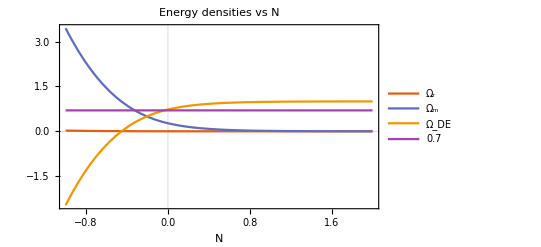

```mathematica
sol1=soln[0,Subscript[Ω, r],Subscript[Ω, m],X,Y,ξ,g,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]];
tfinal=100;

Plot[Evaluate[{Ωr[t],Ωm[t],1-(Ωr[t]+Ωm[t]),0.7}/.sol1],{t,-1,2},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_r","Ω_m","Ω_DE","0.7"},LabelStyle->7,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-0.11,0.82}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

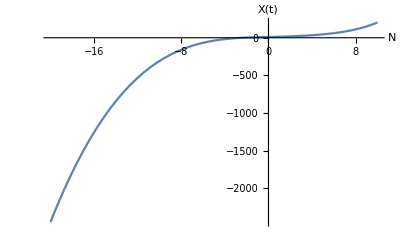

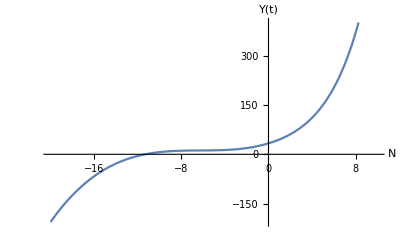

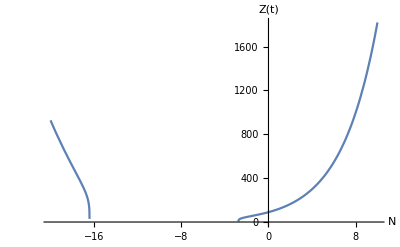

```mathematica
Plot[Evaluate[{x[t]}/.sol1],{t,-20,10},AxesLabel->{"N","X(t)"}]
Plot[Evaluate[{y[t]}/.sol1],{t,-20,10},AxesLabel->{"N","Y(t)"}]
Plot[Evaluate[{z[t]}/.sol1],{t,-20,10},AxesLabel->{"N","Z(t)"}]
```

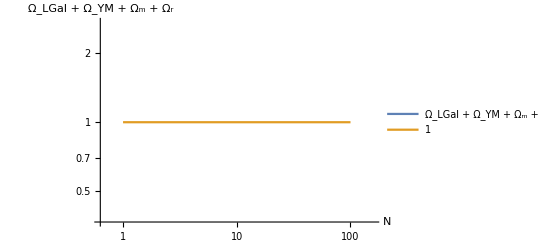

```mathematica
LogLogPlot[Evaluate[{Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4+ξ (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)+Ωr[t]+Ωm[t],1}/.sol1],{t,1,tfinal},PlotRange->All,AxesLabel->{"N","Ω_LGal + Ω_YM + Ω_m + Ω_r"},PlotLegends->LineLegend[{"Ω_LGal + Ω_YM + Ω_m + Ω_r","1"}]]
```

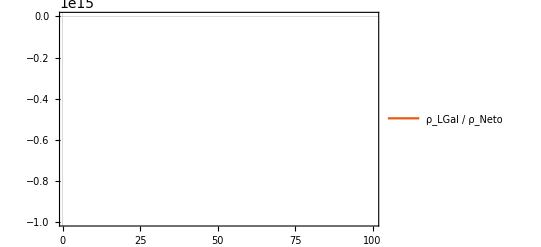

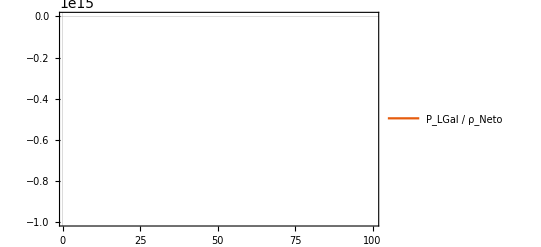

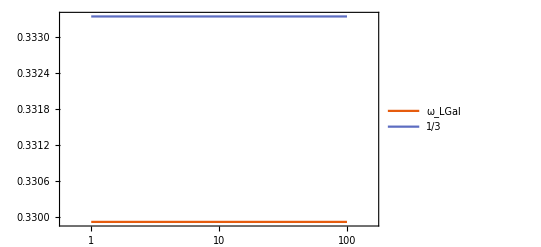

```mathematica
Plot[Evaluate[{Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"ρ_LGal / ρ_Neto"}]]

Plot[Evaluate[{ -((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"P_LGal / ρ_Neto"}]]

LogLinearPlot[Evaluate[{(-((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4))))/(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4),1/3}/.sol1],{t,1,tfinal}, PlotRange->All,PlotTheme->"Scientific",PlotLegends->LineLegend[{"ω_LGal","1/3"}]]
```

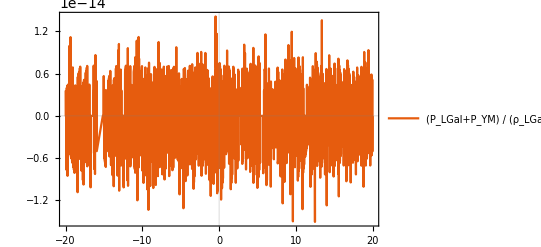

```mathematica
Plot[Evaluate[( -((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))+(ξ/3) (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4))/(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4+ξ (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4))/.sol1],{t,-20,20}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"(P_LGal+P_YM) / (ρ_LGal+ρ_YM)"}]]
```

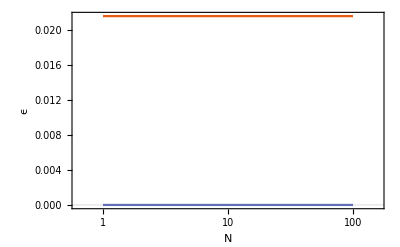

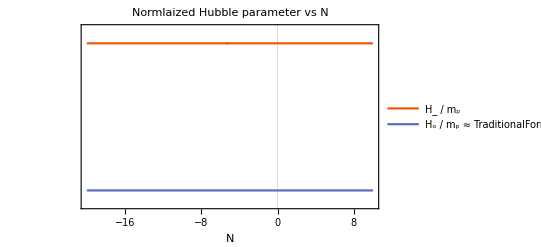

```mathematica
LogLinearPlot[Evaluate[{(304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)),0}/.sol1],{t,1,tfinal},PlotTheme->"Scientific", PlotRange->All,AxesLabel->{"N","ϵ"}]

LogPlot[Evaluate[{y[t]^2/z[t]^2,(β/γ)^2}/.sol1],{t,-20,10},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Normlaized Hubble parameter  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"H_ / m_p",StringForm["H_o / m_p ≈  ``",(β/γ)^2//ScientificForm]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.43)/2-0.12,0.78}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

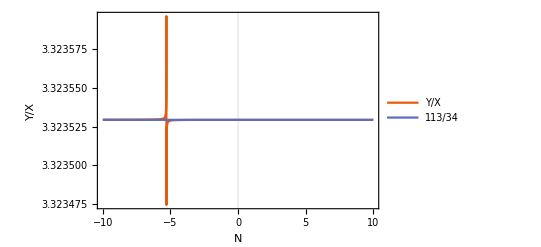

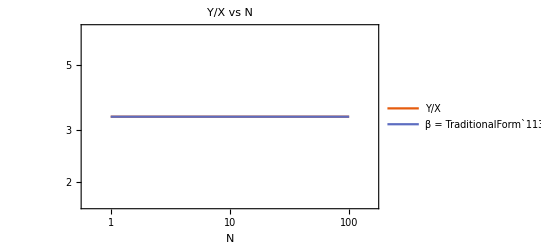

```mathematica
Plot[Evaluate[{y[t]/x[t],β}/.sol1],{t,-10,10},PlotTheme->"Scientific",PlotRange->All,AxesLabel->{"N","Y/X"},PlotLegends->LineLegend[{"Y/X",β}]]

LogLogPlot[Evaluate[{y[t]/x[t],Abs[β]}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Y/X  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Y/X",StringForm["β = `` ≃ ``",Rationalize[β],N[β]]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.28)/2-0.12,0.78}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

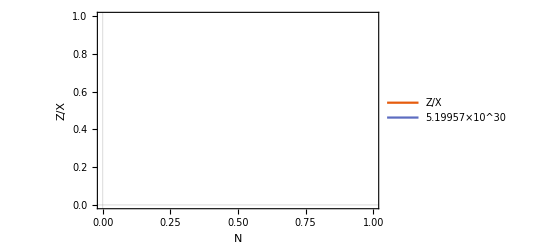

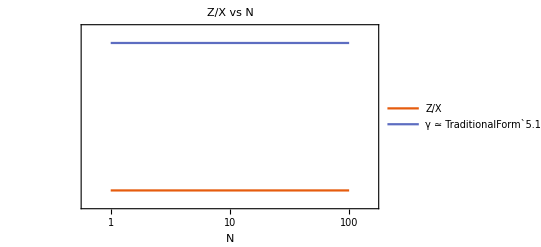

```mathematica
Plot[Evaluate[{z[t]/x[t],γ}/.sol1],{t,0,tfinal},PlotTheme->"Scientific",AxesLabel->{"N","Z/X"},PlotRange->All,PlotLegends->LineLegend[{"Z/X",γ}]]

LogLogPlot[Evaluate[{z[t]/x[t],γ}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Z/X  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Z/X",StringForm["γ ≃ ``",N[γ]]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.35)/2-0.12,0.25}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

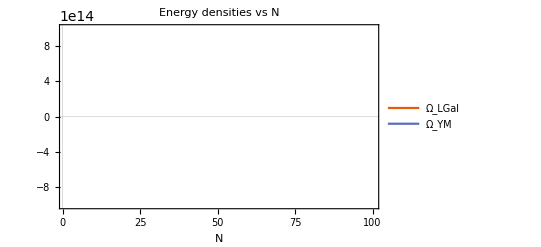

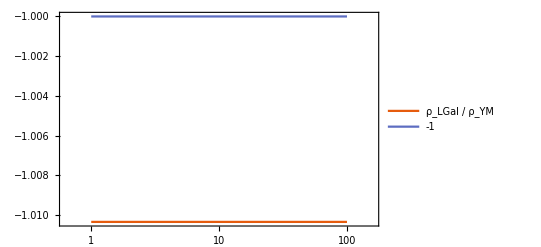

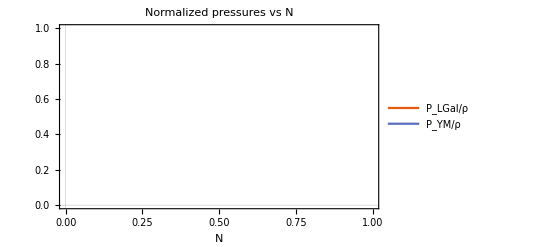

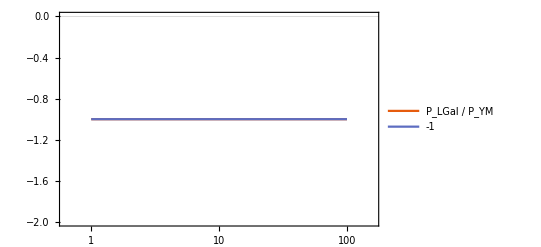

```mathematica
Plot[Evaluate[{(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4),(x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)ξ}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_LGal","Ω_YM"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{(0.1)/2+0.12,0.23}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]


LogLinearPlot[{Evaluate[{(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4)/((x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)ξ)}/.sol1],-1},{t,1,tfinal},PlotRange->All,PlotTheme->"Scientific",PlotLegends->LineLegend[{"ρ_LGal / ρ_YM","-1"}]]


Plot[Evaluate[{(2 (-152064 Subscript[χ, 5]^2 y[t]^9 (x[t]+y[t])^6 (-1+2 Subscript[θ, 1] y[t]^2)+24 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^2 z[t]^4 (11 ξ x[t]^2+22 ξ x[t] y[t]+11 ξ y[t]^2+110 α x[t]^2 y[t]^2+22 κ x[t]^2 y[t]^2-88 Subscript[χ, 4] x[t]^2 y[t]^2+220 α x[t] y[t]^3+44 κ x[t] y[t]^3-176 Subscript[χ, 4] x[t] y[t]^3+7368 α x[t]^2 y[t]^3+2304 Subscript[θ, 4] x[t]^2 y[t]^3+840 κ x[t]^2 y[t]^3+48 Subscript[χ, 4] x[t]^2 y[t]^3+110 α y[t]^4+22 κ y[t]^4-88 Subscript[χ, 4] y[t]^4-368 α x[t] y[t]^4+1792 Subscript[θ, 4] x[t] y[t]^4+816 κ x[t] y[t]^4+96 Subscript[χ, 4] x[t] y[t]^4+232 α y[t]^5+1024 Subscript[θ, 4] y[t]^5+456 κ y[t]^5+48 Subscript[χ, 4] y[t]^5+1992 α ξ x[t]^2 y[t]^5+384 Subscript[θ, 4] ξ x[t]^2 y[t]^5+120 κ ξ x[t]^2 y[t]^5+3984 α ξ x[t] y[t]^6+768 Subscript[θ, 4] ξ x[t] y[t]^6+240 κ ξ x[t] y[t]^6+1992 α ξ y[t]^7+384 Subscript[θ, 4] ξ y[t]^7+120 κ ξ y[t]^7+8 Subscript[χ, 3] y[t]^2 (x[t]+y[t])^2 (-11+6 y[t])+16 Subscript[θ, 1]^2 y[t]^2 (2 x[t] y[t] (11+16 y[t])+y[t]^2 (11+20 y[t])+x[t]^2 (11+24 y[t]))-144 Subscript[χ, 1] y[t] z[t]^4-144 Subscript[χ, 2] y[t] z[t]^4+3984 g^2 α ξ y[t]^5 z[t]^4+768 g^2 Subscript[θ, 4] ξ y[t]^5 z[t]^4+240 g^2 κ ξ y[t]^5 z[t]^4-2 Subscript[θ, 1] y[t]^2 (11 ξ x[t]^2+22 ξ x[t] y[t]+24 ξ x[t]^2 y[t]+11 ξ y[t]^2+48 ξ x[t] y[t]^2+2398 α x[t]^2 y[t]^2+286 κ x[t]^2 y[t]^2-88 Subscript[χ, 4] x[t]^2 y[t]^2+24 ξ y[t]^3+4796 α x[t] y[t]^3+572 κ x[t] y[t]^3-176 Subscript[χ, 4] x[t] y[t]^3+15336 α x[t]^2 y[t]^3+1320 κ x[t]^2 y[t]^3+48 Subscript[χ, 4] x[t]^2 y[t]^3+2398 α y[t]^4+286 κ y[t]^4-88 Subscript[χ, 4] y[t]^4+10256 α x[t] y[t]^4+1456 κ x[t] y[t]^4+96 Subscript[χ, 4] x[t] y[t]^4+6872 α y[t]^5+856 κ y[t]^5+48 Subscript[χ, 4] y[t]^5+8 Subscript[χ, 3] y[t]^2 (x[t]+y[t])^2 (-11+6 y[t])+64 Subscript[θ, 4] y[t]^2 (2 x[t] y[t] (11+30 y[t])+y[t]^2 (11+36 y[t])+x[t]^2 (11+60 y[t]))+48 g^2 ξ y[t] z[t]^4-144 Subscript[χ, 1] y[t] z[t]^4-144 Subscript[χ, 2] y[t] z[t]^4))+z[t]^8 (307 α ξ x[t]^2 y[t]^2+35 κ ξ x[t]^2 y[t]^2+2 ξ Subscript[χ, 3] x[t]^2 y[t]^2+2 ξ Subscript[χ, 4] x[t]^2 y[t]^2-154 α ξ x[t] y[t]^3+18 κ ξ x[t] y[t]^3+4 ξ Subscript[χ, 3] x[t] y[t]^3+4 ξ Subscript[χ, 4] x[t] y[t]^3-129 α ξ y[t]^4+3 κ ξ y[t]^4+2 ξ Subscript[χ, 3] y[t]^4+2 ξ Subscript[χ, 4] y[t]^4+2030 α^2 x[t]^2 y[t]^4+636 α κ x[t]^2 y[t]^4+46 κ^2 x[t]^2 y[t]^4+83 α ξ^2 x[t]^2 y[t]^4+5 κ ξ^2 x[t]^2 y[t]^4-1188 α Subscript[χ, 3] x[t]^2 y[t]^4-132 κ Subscript[χ, 3] x[t]^2 y[t]^4-16 Subscript[χ, 3]^2 x[t]^2 y[t]^4-1188 α Subscript[χ, 4] x[t]^2 y[t]^4-132 κ Subscript[χ, 4] x[t]^2 y[t]^4-32 Subscript[χ, 3] Subscript[χ, 4] x[t]^2 y[t]^4-16 Subscript[χ, 4]^2 x[t]^2 y[t]^4-1540 α^2 x[t] y[t]^5-128 α κ x[t] y[t]^5+36 κ^2 x[t] y[t]^5+166 α ξ^2 x[t] y[t]^5+10 κ ξ^2 x[t] y[t]^5+2104 α Subscript[χ, 3] x[t] y[t]^5-40 κ Subscript[χ, 3] x[t] y[t]^5-32 Subscript[χ, 3]^2 x[t] y[t]^5+2104 α Subscript[χ, 4] x[t] y[t]^5-40 κ Subscript[χ, 4] x[t] y[t]^5-64 Subscript[χ, 3] Subscript[χ, 4] x[t] y[t]^5-32 Subscript[χ, 4]^2 x[t] y[t]^5+7238 α^2 y[t]^6-76 α κ y[t]^6-90 κ^2 y[t]^6+83 α ξ^2 y[t]^6+5 κ ξ^2 y[t]^6+636 α Subscript[χ, 3] y[t]^6-68 κ Subscript[χ, 3] y[t]^6-16 Subscript[χ, 3]^2 y[t]^6+636 α Subscript[χ, 4] y[t]^6-68 κ Subscript[χ, 4] y[t]^6-32 Subscript[χ, 3] Subscript[χ, 4] y[t]^6-16 Subscript[χ, 4]^2 y[t]^6-4578 α^2 ξ x[t]^2 y[t]^6-1032 α κ ξ x[t]^2 y[t]^6-62 κ^2 ξ x[t]^2 y[t]^6-664 α ξ Subscript[χ, 3] x[t]^2 y[t]^6-40 κ ξ Subscript[χ, 3] x[t]^2 y[t]^6-664 α ξ Subscript[χ, 4] x[t]^2 y[t]^6-40 κ ξ Subscript[χ, 4] x[t]^2 y[t]^6-9156 α^2 ξ x[t] y[t]^7-2064 α κ ξ x[t] y[t]^7-124 κ^2 ξ x[t] y[t]^7-1328 α ξ Subscript[χ, 3] x[t] y[t]^7-80 κ ξ Subscript[χ, 3] x[t] y[t]^7-1328 α ξ Subscript[χ, 4] x[t] y[t]^7-80 κ ξ Subscript[χ, 4] x[t] y[t]^7-4578 α^2 ξ y[t]^8-1032 α κ ξ y[t]^8-62 κ^2 ξ y[t]^8-664 α ξ Subscript[χ, 3] y[t]^8-40 κ ξ Subscript[χ, 3] y[t]^8-664 α ξ Subscript[χ, 4] y[t]^8-40 κ ξ Subscript[χ, 4] y[t]^8-6 ξ Subscript[χ, 1] z[t]^4-6 ξ Subscript[χ, 2] z[t]^4-416 g^2 α ξ y[t]^2 z[t]^4-48 g^2 κ ξ y[t]^2 z[t]^4+2436 α Subscript[χ, 1] y[t]^2 z[t]^4+276 κ Subscript[χ, 1] y[t]^2 z[t]^4+772 α Subscript[χ, 2] y[t]^2 z[t]^4+84 κ Subscript[χ, 2] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 3] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 3] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 4] y[t]^2 z[t]^4+166 g^2 α ξ^2 y[t]^4 z[t]^4+10 g^2 κ ξ^2 y[t]^4 z[t]^4-9156 g^2 α^2 ξ y[t]^6 z[t]^4-2064 g^2 α κ ξ y[t]^6 z[t]^4-124 g^2 κ^2 ξ y[t]^6 z[t]^4-1328 g^2 α ξ Subscript[χ, 3] y[t]^6 z[t]^4-80 g^2 κ ξ Subscript[χ, 3] y[t]^6 z[t]^4-1328 g^2 α ξ Subscript[χ, 4] y[t]^6 z[t]^4-80 g^2 κ ξ Subscript[χ, 4] y[t]^6 z[t]^4-512 Subscript[θ, 4]^2 y[t]^6 (1+ξ x[t]^2+2 ξ x[t] y[t]+ξ y[t]^2+2 g^2 ξ z[t]^4)+8 Subscript[θ, 1]^2 y[t]^2 (2 ξ x[t]^2-ξ y[t]^2+406 α x[t]^2 y[t]^2+46 κ x[t]^2 y[t]^2+12 Subscript[χ, 4] x[t]^2 y[t]^2-308 α x[t] y[t]^3+36 κ x[t] y[t]^3+24 Subscript[χ, 4] x[t] y[t]^3+4 Subscript[χ, 4] y[t]^4+64 Subscript[θ, 4] x[t] y[t]^2 (2 x[t]+y[t])+4 Subscript[χ, 3] y[t]^2 (3 x[t]^2+6 x[t] y[t]+y[t]^2)-8 g^2 ξ z[t]^4+36 Subscript[χ, 1] z[t]^4+4 Subscript[χ, 2] z[t]^4)-2 Subscript[θ, 1] y[t]^2 (ξ^2 x[t]^2+2 ξ^2 x[t] y[t]+ξ^2 y[t]^2+545 α ξ x[t]^2 y[t]^2+45 κ ξ x[t]^2 y[t]^2-6 ξ Subscript[χ, 4] x[t]^2 y[t]^2-342 α ξ x[t] y[t]^3-2 κ ξ x[t] y[t]^3-12 ξ Subscript[χ, 4] x[t] y[t]^3-389 α ξ y[t]^4-17 κ ξ y[t]^4-6 ξ Subscript[χ, 4] y[t]^4+44254 α^2 x[t]^2 y[t]^4+10292 α κ x[t]^2 y[t]^4+598 κ^2 x[t]^2 y[t]^4+556 α Subscript[χ, 4] x[t]^2 y[t]^4-4 κ Subscript[χ, 4] x[t]^2 y[t]^4-16 Subscript[χ, 4]^2 x[t]^2 y[t]^4-33572 α^2 x[t] y[t]^5-80 α κ x[t] y[t]^5+468 κ^2 x[t] y[t]^5+5592 α Subscript[χ, 4] x[t] y[t]^5+216 κ Subscript[χ, 4] x[t] y[t]^5-32 Subscript[χ, 4]^2 x[t] y[t]^5+16786 α^2 y[t]^6-1500 α κ y[t]^6-54 κ^2 y[t]^6+1052 α Subscript[χ, 4] y[t]^6-20 κ Subscript[χ, 4] y[t]^6-16 Subscript[χ, 4]^2 y[t]^6-16 Subscript[χ, 3]^2 y[t]^4 (x[t]+y[t])^2-512 Subscript[θ, 4]^2 y[t]^4 (-8 x[t]^2-4 x[t] y[t]+y[t]^2)+2 g^2 ξ^2 z[t]^4-6 ξ Subscript[χ, 1] z[t]^4-6 ξ Subscript[χ, 2] z[t]^4-1932 g^2 α ξ y[t]^2 z[t]^4-148 g^2 κ ξ y[t]^2 z[t]^4+9156 α Subscript[χ, 1] y[t]^2 z[t]^4+612 κ Subscript[χ, 1] y[t]^2 z[t]^4+2180 α Subscript[χ, 2] y[t]^2 z[t]^4+100 κ Subscript[χ, 2] y[t]^2 z[t]^4-16 g^2 ξ Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 4] y[t]^2 z[t]^4-2 Subscript[χ, 3] y[t]^2 (3 ξ x[t]^2+6 ξ x[t] y[t]+3 ξ y[t]^2-278 α x[t]^2 y[t]^2+2 κ x[t]^2 y[t]^2-2796 α x[t] y[t]^3-108 κ x[t] y[t]^3-526 α y[t]^4+10 κ y[t]^4+16 Subscript[χ, 4] y[t]^2 (x[t]+y[t])^2+8 g^2 ξ z[t]^4-24 Subscript[χ, 1] z[t]^4-24 Subscript[χ, 2] z[t]^4)+32 Subscript[θ, 4] y[t]^2 (4 ξ x[t]^2-ξ x[t] y[t]-2 ξ y[t]^2+842 α x[t]^2 y[t]^2+98 κ x[t]^2 y[t]^2-90 α x[t] y[t]^3+62 κ x[t] y[t]^3+24 Subscript[χ, 3] x[t] y[t]^3+24 Subscript[χ, 4] x[t] y[t]^3-32 α y[t]^4-12 κ y[t]^4-14 g^2 ξ z[t]^4+60 Subscript[χ, 1] z[t]^4+12 Subscript[χ, 2] z[t]^4))-16 Subscript[θ, 4] y[t]^2 (-6 ξ x[t]^2-2 ξ x[t] y[t]-40 α x[t]^2 y[t]^2-8 κ x[t]^2 y[t]^2-ξ^2 x[t]^2 y[t]^2-20 α x[t] y[t]^3-4 κ x[t] y[t]^3-2 ξ^2 x[t] y[t]^3-60 α y[t]^4+28 κ y[t]^4-ξ^2 y[t]^4+198 α ξ x[t]^2 y[t]^4+22 κ ξ x[t]^2 y[t]^4+396 α ξ x[t] y[t]^5+44 κ ξ x[t] y[t]^5+198 α ξ y[t]^6+22 κ ξ y[t]^6+8 g^2 ξ z[t]^4-48 Subscript[χ, 1] z[t]^4-16 Subscript[χ, 2] z[t]^4-2 g^2 ξ^2 y[t]^2 z[t]^4+396 g^2 α ξ y[t]^4 z[t]^4+44 g^2 κ ξ y[t]^4 z[t]^4+8 Subscript[χ, 3] (2 ξ x[t] y[t]^5+x[t]^2 y[t]^2 (3+ξ y[t]^2)+y[t]^4 (1+ξ y[t]^2+2 g^2 ξ z[t]^4))+8 Subscript[χ, 4] (2 ξ x[t] y[t]^5+x[t]^2 y[t]^2 (3+ξ y[t]^2)+y[t]^4 (1+ξ y[t]^2+2 g^2 ξ z[t]^4))))))/(3 z[t]^4 (-576 Subscript[χ, 5] y[t]^5 (x[t]+y[t])^2 (-1-2 Subscript[θ, 1] y[t]^2+166 α y[t]^4+32 Subscript[θ, 4] y[t]^4+10 κ y[t]^4)+(ξ+10 α y[t]^2+16 Subscript[θ, 1]^2 y[t]^2+2 κ y[t]^2-8 Subscript[χ, 4] y[t]^2-166 α ξ y[t]^4-32 Subscript[θ, 4] ξ y[t]^4-10 κ ξ y[t]^4+9156 α^2 y[t]^6+6336 α Subscript[θ, 4] y[t]^6+1024 Subscript[θ, 4]^2 y[t]^6+2064 α κ y[t]^6+704 Subscript[θ, 4] κ y[t]^6+124 κ^2 y[t]^6+1328 α Subscript[χ, 4] y[t]^6+256 Subscript[θ, 4] Subscript[χ, 4] y[t]^6+80 κ Subscript[χ, 4] y[t]^6+8 Subscript[χ, 3] y[t]^2 (-1+32 Subscript[θ, 4] y[t]^4+2 (83 α+5 κ) y[t]^4)-2 Subscript[θ, 1] (-ξ y[t]^2+406 α y[t]^4+128 Subscript[θ, 4] y[t]^4+46 κ y[t]^4+8 Subscript[χ, 3] y[t]^4+8 Subscript[χ, 4] y[t]^4)) z[t]^4)),1/3(x[t]^2+2 x[t]y[t]+y[t]^2+2 g^2 z[t]^4)ξ}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Normalized pressures  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"P_LGal/ρ","P_YM/ρ"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{(0.1)/2+0.12,0.23}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]

LogLinearPlot[Evaluate[{(-((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4))))/((ξ/3)(x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)),-1}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLegends->LineLegend[{"P_LGal / P_YM","-1"}]]
```

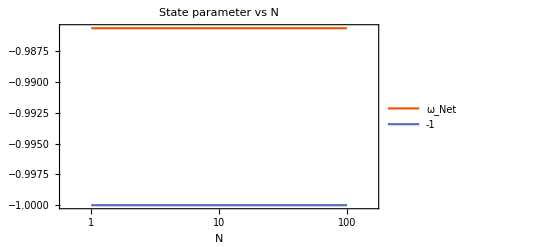

```mathematica
LogLinearPlot[Evaluate[{(2/3)((304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))-1,-1}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["State parameter  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"ω_Net","-1"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.05)/2-0.12,0.8}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]

(* (2/3)ϵ-1 = Subscript[ω, Neto] , de la definición de ϵ, Friedmann y continuidad. Es un caso particular de 
(2/3)ϵ = (Subscript[ρ, Neto]+Subscript[P, Neto])/Subscript[ρ, Neto] [ válido para fluídos perfectos en FLRW plano ] -> De aquí tmbn sale la condición de Gauge-Flation. *)
```

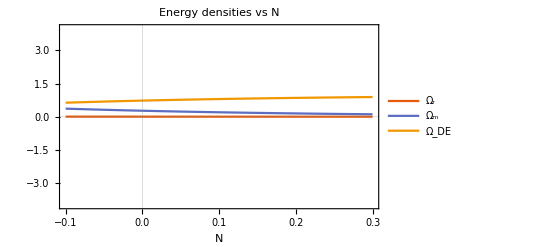

```mathematica
Plot[Evaluate[{Ωr[t],Ωm[t],1-(Ωr[t]+Ωm[t])(*,0.3107,0.0046*)}/.sol1],{t,-0.1,0.3},PlotTheme->"Scientific",PlotRange->{-4,4},PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_r","Ω_m","Ω_DE","Ω_m=0.3107","Ω_r=0.0046"},LabelStyle->7,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-0.11,0.82}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

## 4. Ecuaciones de estado ( programado para ejecutarse justo después de “Inicialización” )

```mathematica
Clear@@DeleteCases[Names@"`*","ΩGal"|"Ωym"|"PGal"|"Pym"|"ϵ"];
```

```mathematica
β=(203+64 Subscript[Q, 4]+23 Subscript[Q, κ])/(77-16 Subscript[Q, 4]-9 Subscript[Q, κ]);
```

```mathematica
γ=-((-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4))/((-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4 (g^2 ξ-6 Subscript[χ, 1]))^(1/4));
```

```mathematica
κ=Subscript[Q, κ]*α;
Subscript[θ, 4]=Subscript[Q, 4]*α;
Subscript[χ, 1]=Subscript[Q, 1]*α;
Subscript[χ, 2]=0;
Subscript[χ, 3]=0;
Subscript[χ, 4]=0;
Subscript[χ, 5]=0;
Subscript[θ, 1]=0;
```

```mathematica
Z=γ*X;
Y=β*X;
```

```mathematica
Limit[ΩGal/Ωym,X-> Infinity]
```

-1

```mathematica
Limit[PGal/Pym,X-> Infinity]
```

-1

```mathematica
wL4=Limit[PGal/ΩGal,X-> Infinity]
```

1/3

```mathematica
wNeto=Limit[(2/3)ϵ-1 ,X-> Infinity]
```

-1

## Caracterización de puntos críticos / Viabilidad de inflación ( esto solo se hizo para L41 + L42 con κ = 81α )

### 1er punto crítico: [ OK ] - ϵ = 0.778761 - ( Punto de silla con Bifurcación en λ_3 ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"}]
Solve[eps==1, α]
MinValue[ϵ,α] //N
```

g<0

α<0

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

ϵ

-Graphics-

{}

ϵ

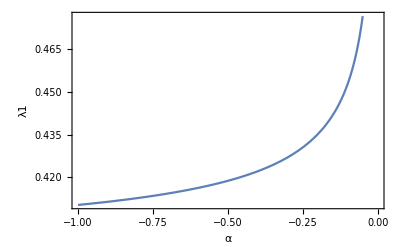

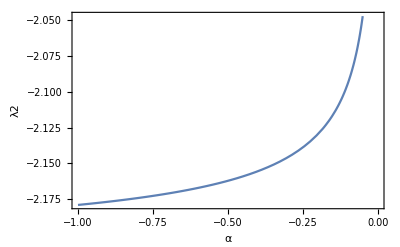

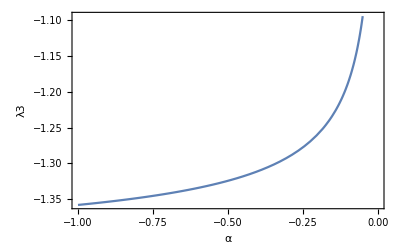

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-1,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-1,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-1,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α] 
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 2.ba punto crítico: [ NO ] porque Y es imaginario, ϵ = 0.757151 .

g<0

α<0

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

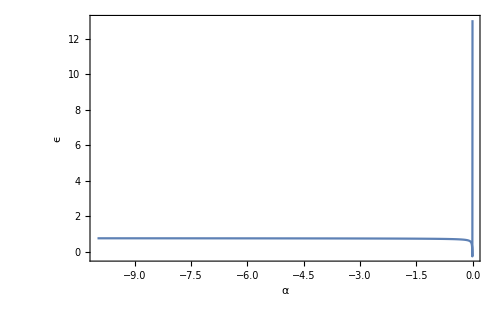

0.757151

```mathematica
Clear[X,Y,Z,α,g]
g<0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
α=-4; eps//N
```

### 3.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=0
X=0
Y=-1
Z=0
eps=FullSimplify[ϵ]
```

g<0

0

0

-1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 4.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=0
X=0
Y=1
Z=0
eps=FullSimplify[ϵ]
```

g<0

0

0

1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 5.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

g<0

0<α<1/4016

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

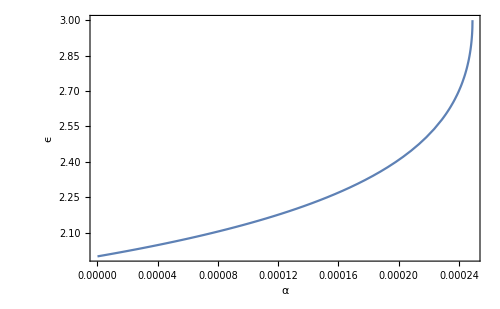

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,1]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

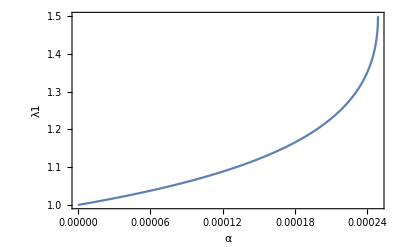

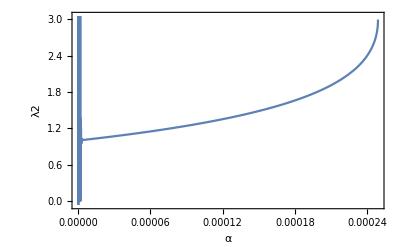

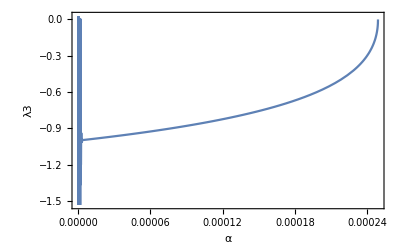

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

### 6.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g<0

0<α<1/4016

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 7.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Repulsor ) .

g<0

0<α<1/4016

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

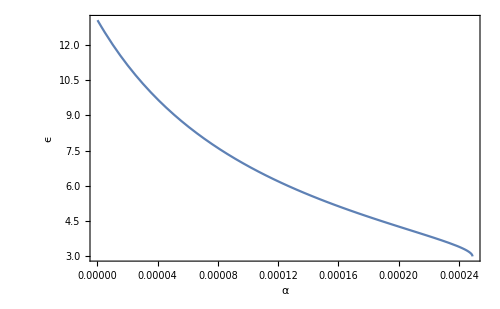

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

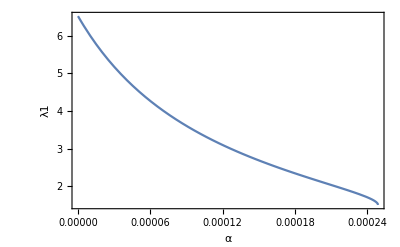

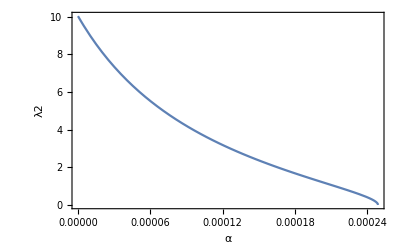

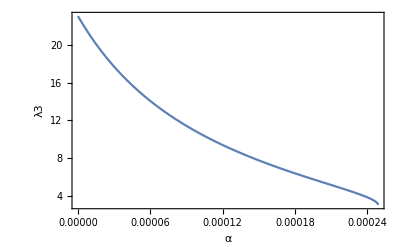

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α+(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

### 8.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Repulsor ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,4]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g<0

0<α<1/4016

0

-(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α+(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 9.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=1/4016
X=0
Y=-Sqrt[2]
Z=ToRadicals[Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
```

g<0

1/4016

0

-√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 10.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=1/4016
X=0
Y=Sqrt[2]
Z=ToRadicals[Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
```

g<0

1/4016

0

√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 11.ba punto crítico: [ OK pero ϵ = 0.778761 ] - ( Punto de silla con Bifurcación en λ_3 ) .

0

α<0

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

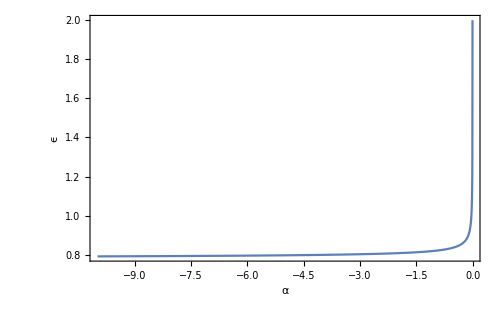

{{α→-301/10000}}

0.778761

```mathematica
Clear[X,Y,Z,α,g]
g=0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,1]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
MinValue[ϵ,α]//N
```

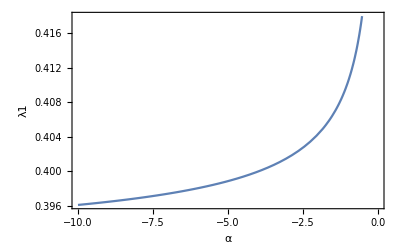

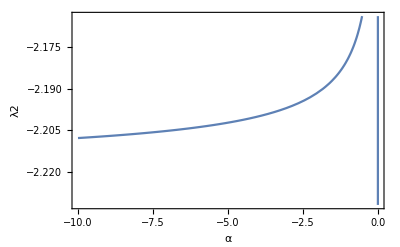

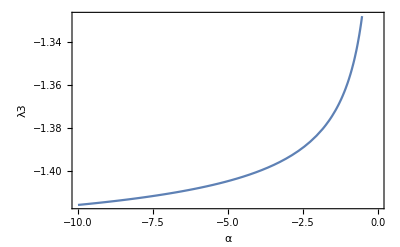

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-10,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-10,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-10,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α]
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 12.ba punto crítico: [ OK pero ϵ = 0.778761 ] - ( Punto de silla con Bifurcación en λ_3 ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,2]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
MinValue[ϵ,α]//N
```

0

α<0

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

0.778761

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-10,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-10,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-10,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α]
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 13.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=0
X=0
Y=-1
Z=0
eps=FullSimplify[ϵ]
```

0

0

0

-1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 14.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=0
X=0
Y=1
Z=0
eps=FullSimplify[ϵ]
```

0

0

0

1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 15.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,1]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
```

0

0<α<1/4016

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 16.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,2]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
```

0

0<α<1/4016

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 17.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,3]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

0

0<α<1/4016

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 18.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,4]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

0

0<α<1/4016

0

-(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 19.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=1/4016
X=0
Y=-Sqrt[2]
Z=0
eps=FullSimplify[ϵ]
```

0

1/4016

0

-√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 20.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=1/4016
X=0
Y=Sqrt[2]
Z=0
eps=FullSimplify[ϵ]
```

0

1/4016

0

√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 21.ba punto crítico: [ OK pero ϵ = 0.778761 ] - ( Punto de silla con Bifurcación en λ_3 ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
MinValue[ϵ,α]//N
```

g>0

α<0

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

0.778761

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-1,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-1,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-1,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α] 
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 22.ba punto crítico: [ NO ] porque Y es imaginario, ϵ = 0.757151 .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
α=-4; ϵ//N
```

g>0

α<0

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

0.757151

### 23.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=0
X=0
Y=-1
Z=0
eps=FullSimplify[ϵ]
```

g>0

0

0

-1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 24.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=0
X=0
Y=1
Z=0
eps=FullSimplify[ϵ]
```

g>0

0

0

1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 25.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,1]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 26.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 27.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 28.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,4]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

-(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 29.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=1/4016
X=0
Y=-Sqrt[2]
Z=Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]
eps=FullSimplify[ϵ]
```

g>0

1/4016

0

-√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 30.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=1/4016
X=0
Y=Sqrt[2]
Z=Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]
eps=FullSimplify[ϵ]
```

g>0

1/4016

0

√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

$Aborted

$Aborted

## Complemento: Rangos viables para Y0, Z0, α que generan un X0 real ( * Esto está en versión de prueba * ) - Puede servir para obtener condiciones iniciales que no generen phantom energy en etapas tempranas.

```mathematica
ClearAll["Global`*"];
κ=81α;
Subscript[θ, 4]=Subscript[Q, 4] α;
Reduce[-1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(-64 X Y^3-32 Y^4) Subscript[θ, 4]+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+2 g^2 Z^4) ξ-12 Z^4 Subscript[χ, 1]==0&&ξ≠ 0&&Y≠ 0&&Z≠ 0,X]/.Subscript[χ, 1]-> (g^2*ξ-η)/6 /.ξ->1//Simplify
```

(1+172 Y^2 α≠0&&(X==-(Y-8 (113+4 Q_4) Y^3 α+√(1-16 (61+2 Q_4) Y^4 α+16 (61869+3960 Q_4+64 Q_4^2) Y^6 α^2-2 Z^4 η-172 Y^2 α (-1+2 Z^4 η)))/(1+172 Y^2 α)||X==(-Y+8 (113+4 Q_4) Y^3 α+√(1-16 (61+2 Q_4) Y^4 α+16 (61869+3960 Q_4+64 Q_4^2) Y^6 α^2-2 Z^4 η-172 Y^2 α (-1+2 Z^4 η)))/(1+172 Y^2 α))&&Y Z≠0)||(α≠0&&(Y==-ⅈ/(2 √43 √α)||Y==ⅈ/(2 √43 √α))&&Q_4==-269/8&&Z≠0&&(g==-(√(1/2-(25 Y^2)/86+g^2 Z^4-Z^4 η))/Z^2||g==(√(1/2-(25 Y^2)/86+g^2 Z^4-Z^4 η))/Z^2))||(α≠0&&(Y==-ⅈ/(2 √43 √α)||Y==ⅈ/(2 √43 √α))&&(269+8 Q_4) Y≠0&&X==(43-294 Y^2-8 Q_4 Y^2-86 Z^4 η)/(538 Y+16 Q_4 Y)&&Z≠0)

```mathematica
Solve[1+172 Y^2 α==0,Y] (* La desigualdad siempre se satisface sobre el campo de los Reales *)
```

{{Y→-ⅈ/(2 √43 √α)},{Y→ⅈ/(2 √43 √α)}}

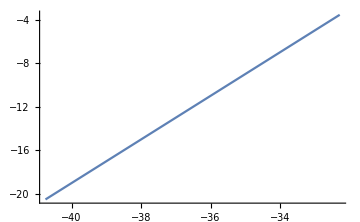
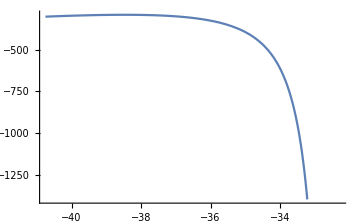
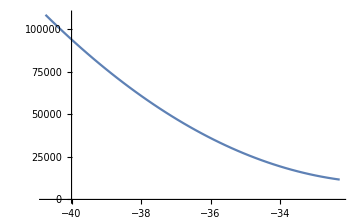
Grid[{-Graphics-,-Graphics-,-Graphics-}]

En lo relativo a Q_4 todos los polinomios involucrados son monótonos, por consiguiente, basta evaluar en los extremos

1+172 Q_Y^2 α^3+(328. Q_Y^4+5.05968×10^-119 Q_z^4) α^5+(108400. Q_Y^6+8.70266×10^-117 Q_Y^2 Q_z^4) α^8

1+172 Q_Y^2 α^3+(57. Q_Y^4+2.57554×10^-90 Q_z^4) α^5+(11653. Q_Y^6+4.42993×10^-88 Q_Y^2 Q_z^4) α^8

```mathematica
Clear[Subscript[Q, 4],Subscript[Q, z],Subscript[Q, Y]];
Qi=-40.75; Qf= -32.28125;Z=Subscript[Q, z]*α;Y=Subscript[Q, Y] α; η=(2 Ho^2 (111054855+11067816 Subscript[Q, 4]+368320 Subscript[Q, 4]^2+4096 Subscript[Q, 4]^3) α)/(mp^2 (1033+32 Subscript[Q, 4])^2);
DiscriminanteDeX=1-16 (61+2 Subscript[Q, 4]) Y^4 α+16 (61869+3960 Subscript[Q, 4]+64 Subscript[Q, 4]^2) Y^6 α^2-2 Z^4 η-172 Y^2 α (-1+2 Z^4 η)//Simplify;

Ho=10^(-42);
mp=2.435*10^(18);

Collect[DiscriminanteDeX,{Y,α}];
Grid[{Plot[61+2 Subscript[Q, 4],{Subscript[Q, 4],Qi,Qf},ImageSize->Medium],Plot[4*(111054855+11067816 Subscript[Q, 4]+368320 Subscript[Q, 4]^2+4096 Subscript[Q, 4]^3)/((1033+32 Subscript[Q, 4])^2),{Subscript[Q, 4],Qi,Qf},ImageSize->Medium],
Plot[16 (61869+3960 Subscript[Q, 4]+64 Subscript[Q, 4]^2),{Subscript[Q, 4],Qi,Qf},ImageSize->Medium]}]

Print["En lo relativo a Q_4 todos los polinomios involucrados son monótonos, por consiguiente, basta evaluar en los extremos"]

Subscript[Q, 4]=Qi; Collect[DiscriminanteDeX,{Y,α}]
Subscript[Q, 4]=Qf-10^(-14); Collect[DiscriminanteDeX,{Y,α}]
```

```mathematica
n=37;
Grid[{RegionPlot3D[1+172 Subscript[Q, Y]^2 α^3+(328. Subscript[Q, Y]^4+5.05968317950491*^-119 Subscript[Q, z]^4) α^5+(108400. Subscript[Q, Y]^6+8.702655068748445*^-117 Subscript[Q, Y]^2 Subscript[Q, z]^4) α^8≥ 0,{Subscript[Q, Y],-10^n,10^n},{Subscript[Q, z],-10^n,10^n},{α,-10^n,10^n},ImageSize->Medium,Mesh->None,PlotStyle->Directive[Opacity[0.5]]],
RegionPlot3D[1+172 Subscript[Q, Y]^2 α^3+(57.00000000000023 Subscript[Q, Y]^4+2.575542677558768*^-90 Subscript[Q, z]^4) α^5+(11653. Subscript[Q, Y]^6+4.4299334054010804*^-88 Subscript[Q, Y]^2 Subscript[Q, z]^4) α^8≥ 0,{Subscript[Q, Y],-10^n,10^n},{Subscript[Q, z],-10^n,10^n},{α,-10^n,10^n},ImageSize->Medium,Mesh->None,PlotStyle->Directive[Opacity[0.5]]]}]
```

Grid[{-Graphics3D-,-Graphics3D-}]

```mathematica
Print[];
For[i=0,i<10,i++,Print["ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 )."]] ;Print[];
```

ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 ).

ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 ).

ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 ).

«7 more identical outputs»

$Aborted

$Aborted

1.19442

$Aborted

$Aborted

(-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) α≠0&&(Y==-(√((3 Q_1 √α-√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2)||Y==(√((3 Q_1 √α-√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2)||Y==-(√((3 Q_1 √α+√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2)||Y==(√((3 Q_1 √α+√(308-64 Q_4-36 Q_κ-8 R_3-8 R_4+9 Q_1^2 α))/((-77+16 Q_4+9 Q_κ+2 R_3+2 R_4) √α)))/(√2))&&-89992 Q_1 α-25728 Q_1 Q_4 α+1024 Q_1 Q_4^2 α-5968 Q_1 Q_κ α+1664 Q_1 Q_4 Q_κ α+456 Q_1 Q_κ^2 α-984 Q_1 R_3 α+256 Q_1 Q_4 R_3 α+136 Q_1 Q_κ R_3 α+16 Q_1 R_3^2 α-984 Q_1 R_4 α+256 Q_1 Q_4 R_4 α+136 Q_1 Q_κ R_4 α+32 Q_1 R_3 R_4 α+16 Q_1 R_4^2 α+764302 Y^2 α+316736 Q_4 Y^2 α-19968 Q_4^2 Y^2 α-16384 Q_4^3 Y^2 α+74522 Q_κ Y^2 α-37888 Q_4 Q_κ Y^2 α-19968 Q_4^2 Q_κ Y^2 α-10990 Q_κ^2 Y^2 α-7744 Q_4 Q_κ^2 Y^2 α-954 Q_κ^3 Y^2 α+6020 R_3 Y^2 α-2944 Q_4 R_3 Y^2 α-5120 Q_4^2 R_3 Y^2 α-1736 Q_κ R_3 Y^2 α-4224 Q_4 Q_κ R_3 Y^2 α-860 Q_κ^2 R_3 Y^2 α-56 R_3^2 Y^2 α-512 Q_4 R_3^2 Y^2 α-216 Q_κ R_3^2 Y^2 α-16 R_3^3 Y^2 α+6020 R_4 Y^2 α-2944 Q_4 R_4 Y^2 α-5120 Q_4^2 R_4 Y^2 α-1736 Q_κ R_4 Y^2 α-4224 Q_4 Q_κ R_4 Y^2 α-860 Q_κ^2 R_4 Y^2 α-112 R_3 R_4 Y^2 α-1024 Q_4 R_3 R_4 Y^2 α-432 Q_κ R_3 R_4 Y^2 α-48 R_3^2 R_4 Y^2 α-56 R_4^2 Y^2 α-512 Q_4 R_4^2 Y^2 α-216 Q_κ R_4^2 Y^2 α-48 R_3 R_4^2 Y^2 α-16 R_4^3 Y^2 α+364840 Q_1^2 Y^2 α^2+37760 Q_1^2 Q_4 Y^2 α^2+1024 Q_1^2 Q_4^2 Y^2 α^2-4272 Q_1^2 Q_κ Y^2 α^2-384 Q_1^2 Q_4 Q_κ Y^2 α^2-72 Q_1^2 Q_κ^2 Y^2 α^2-1976 Q_1^2 R_3 Y^2 α^2+256 Q_1^2 Q_4 R_3 Y^2 α^2+168 Q_1^2 Q_κ R_3 Y^2 α^2+16 Q_1^2 R_3^2 Y^2 α^2-1976 Q_1^2 R_4 Y^2 α^2+256 Q_1^2 Q_4 R_4 Y^2 α^2+168 Q_1^2 Q_κ R_4 Y^2 α^2+32 Q_1^2 R_3 R_4 Y^2 α^2+16 Q_1^2 R_4^2 Y^2 α^2-6853 ξ-2272 Q_4 ξ+768 Q_4^2 ξ-662 Q_κ ξ+736 Q_4 Q_κ ξ+171 Q_κ^2 ξ+24 R_3 ξ+128 Q_4 R_3 ξ+56 Q_κ R_3 ξ+4 R_3^2 ξ+24 R_4 ξ+128 Q_4 R_4 ξ+56 Q_κ R_4 ξ+8 R_3 R_4 ξ+4 R_4^2 ξ+50204 Q_1 Y^2 α ξ-5504 Q_1 Q_4 Y^2 α ξ-1024 Q_1 Q_4^2 Y^2 α ξ-4944 Q_1 Q_κ Y^2 α ξ-768 Q_1 Q_4 Q_κ Y^2 α ξ-108 Q_1 Q_κ^2 Y^2 α ξ-1612 Q_1 R_3 Y^2 α ξ-64 Q_1 Q_4 R_3 Y^2 α ξ+12 Q_1 Q_κ R_3 Y^2 α ξ+8 Q_1 R_3^2 Y^2 α ξ-1612 Q_1 R_4 Y^2 α ξ-64 Q_1 Q_4 R_4 Y^2 α ξ+12 Q_1 Q_κ R_4 Y^2 α ξ+16 Q_1 R_3 R_4 Y^2 α ξ+8 Q_1 R_4^2 Y^2 α ξ≠0

Q_4==1/16 (77-9 Q_κ-2 R_3-2 R_4)&&Q_1 α≠0&&(Y==-1/(√3 √Q_1 √α)||Y==1/(√3 √Q_1 √α))&&63364-3656 Q_κ+52 Q_κ^2-744 R_3+24 Q_κ R_3-744 R_4+24 Q_κ R_4-6042 Q_1^2 α+174 Q_1^2 Q_κ α+36 Q_1^2 R_3 α+36 Q_1^2 R_4 α+144 Q_1^4 α^2-960 Q_1 ξ+24 Q_1 Q_κ ξ+12 Q_1 R_3 ξ+12 Q_1 R_4 ξ+45 Q_1^3 α ξ≠0

α≠0&&Q_4==1/8 (-8-3 Q_κ-R_3-R_4)&&6 Q_1 α+ξ≠0&&(Y==-1/(√(6 Q_1 α+ξ))||Y==1/(√(6 Q_1 α+ξ)))&&-62 α+2 Q_κ α+24 Q_1^2 α^2+10 Q_1 α ξ+ξ^2≠0

1
 |  |  |  |